### Start choosing the example:

```mathematica
t=23;
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/salehfh/Downloads/MFGraphs-master/MFGraphs/NonLinearSolver.m"]
```

<|Vertices List→{1,2,3,4,5,6},Adjacency Matrix→{{0,1,1,0,0,0},{0,0,1,0,0,0},{0,0,0,1,1,0},{0,0,0,0,1,1},{0,0,0,0,0,1},{0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{4,U1},{5,U2},{6,U3}},Switching Costs→{}|>

Iterative boolean convert took 17.8758 seconds to terminate

Iterative boolean convert took 0.764182 seconds to terminate

Iterative boolean convert took 0.39588 seconds to terminate

Iterative boolean convert took 0.04863 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {0≤jt38≤5&&0≤jt14≤395/2,<|j24→200,j26→200,j23→0,j25→0,j15→0,j19→0,j21→0,j2→0,j4→200,j1→0,j6→200,j3→0,j5→0,j8→395/2,j10→405/2,j7→0,j12→5,j14→10,j16→365/2,j9→0,j11→0,j18→5,j20→405/2,j13→0,j17→0,j22→15,u16→10,u20→5,u22→0,jt12→200,jt2→0,jt27→365/2,jt34→0,jt36→0,jt39→405/2-jt38,jt4→0,jt42→jt38,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→10,jt51→0,jt52→5,jt54→0,jt6→200,jt7→0,jt8→0,jt9→0,u15→10,u19→5,u21→0,u24→815/2,u26→815/2,jt23→0,jt3→0,jt31→0,jt35→0,jt53→0,u10→5,u11→10,u17→5,u18→0,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u8→10,u9→415/2,jt10→0,jt22→0,jt18→5/2+jt14,jt32→0,jt45→0,u12→5,u13→10,u14→0,u2→815/2,u7→415/2,jt1→0,jt11→0,jt13→0,jt15→200-jt14,jt19→0,jt20→0,jt16→0,u23→815/2,u25→815/2,jt17→395/2-jt14,jt21→0,jt24→0,jt25→5,jt26→10,jt28→0,jt29→0,jt30→0,jt33→0,jt37→0,jt40→0,jt41→5-jt38,jt43→0,jt44→0,u1→815/2|>}

Picked one value for the variable(s) {jt14,jt38}{99,5/2}

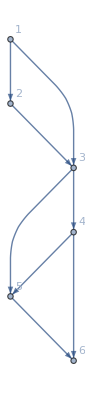
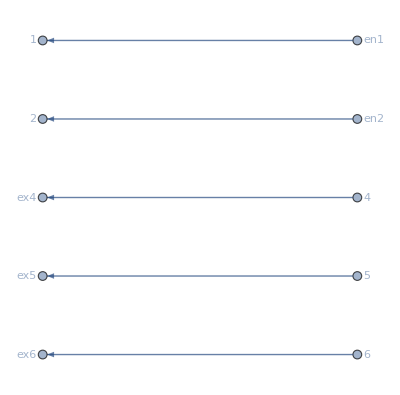
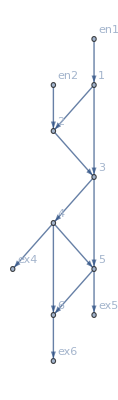
{21.8997,<|Vertices List→{1,2,3,4,5,6},Adjacency Matrix→{{0,1,1,0,0,0},{0,0,1,0,0,0},{0,0,0,1,1,0},{0,0,0,0,1,1},{0,0,0,0,0,1},{0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,200},{2,200}},Exit Vertices and Terminal Costs→{{4,10},{5,5},{6,0}},Switching Costs→{},VL→{1,2,3,4,5,6},AM→{{0,1,1,0,0,0},{0,0,1,0,0,0},{0,0,0,1,1,0},{0,0,0,0,1,1},{0,0,0,0,0,1},{0,0,0,0,0,0}},EVC→{{1,200},{2,200}},EVTC→{{4,10},{5,5},{6,0}},SC→{},BG→-Graphics-,EntranceVertices→{1,2},InwardVertices→<|1→en1,2→en2|>,ExitVertices→{4,5,6},OutwardVertices→<|4→ex4,5→ex5,6→ex6|>,InEdges→{en1->1,en2->2},OutEdges→{4->ex4,5->ex5,6->ex6},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->2,1->3,2->3,3->4,3->5,4->5,4->6,4->ex4,5->6,5->ex5,6->ex6,en1->1,en2->2},BEL→{1->2,1->3,2->3,3->4,3->5,4->5,4->6,5->6},FVL→{1,2,3,4,5,6,en1,en2,ex4,ex5,ex6},jargs→{{1,1->2},{2,1->2},{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{3,3->5},{5,3->5},{4,4->5},{5,4->5},{4,4->6},{6,4->6},{4,4->ex4},{ex4,4->ex4},{5,5->6},{6,5->6},{5,5->ex5},{ex5,5->ex5},{6,6->ex6},{ex6,6->ex6},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},uargs→{{1,1->2},{2,1->2},{1,1->3},{3,1->3},{2,2->3},{3,2->3},{3,3->4},{4,3->4},{3,3->5},{5,3->5},{4,4->5},{5,4->5},{4,4->6},{6,4->6},{4,4->ex4},{ex4,4->ex4},{5,5->6},{6,5->6},{5,5->ex5},{ex5,5->ex5},{6,6->ex6},{ex6,6->ex6},{en1,en1->1},{1,en1->1},{en2,en2->2},{2,en2->2}},AllTransitions→{{1,1->2,1->3},{1,1->2,en1->1},{1,1->3,1->2},{1,1->3,en1->1},{1,en1->1,1->2},{1,en1->1,1->3},{2,1->2,2->3},{2,1->2,en2->2},{2,2->3,1->2},{2,2->3,en2->2},{2,en2->2,1->2},{2,en2->2,2->3},{3,1->3,2->3},{3,1->3,3->4},{3,1->3,3->5},{3,2->3,1->3},{3,2->3,3->4},{3,2->3,3->5},{3,3->4,1->3},{3,3->4,2->3},{3,3->4,3->5},{3,3->5,1->3},{3,3->5,2->3},{3,3->5,3->4},{4,3->4,4->5},{4,3->4,4->6},{4,3->4,4->ex4},{4,4->5,3->4},{4,4->5,4->6},{4,4->5,4->ex4},{4,4->6,3->4},{4,4->6,4->5},{4,4->6,4->ex4},{4,4->ex4,3->4},{4,4->ex4,4->5},{4,4->ex4,4->6},{5,3->5,4->5},{5,3->5,5->6},{5,3->5,5->ex5},{5,4->5,3->5},{5,4->5,5->6},{5,4->5,5->ex5},{5,5->6,3->5},{5,5->6,4->5},{5,5->6,5->ex5},{5,5->ex5,3->5},{5,5->ex5,4->5},{5,5->ex5,5->6},{6,4->6,5->6},{6,4->6,6->ex6},{6,5->6,4->6},{6,5->6,6->ex6},{6,6->ex6,4->6},{6,6->ex6,5->6}},EntryArgs→{{1,en1->1},{2,en2->2}},EntryDataAssociation→<|{1,en1->1}→200,{2,en2->2}→200|>,ExitCosts→<|ex4→10,ex5→5,ex6→0|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26},jvars→<|{1,1->2}→j1,{2,1->2}→j2,{1,1->3}→j3,{3,1->3}→j4,{2,2->3}→j5,{3,2->3}→j6,{3,3->4}→j7,{4,3->4}→j8,{3,3->5}→j9,{5,3->5}→j10,{4,4->5}→j11,{5,4->5}→j12,{4,4->6}→j13,{6,4->6}→j14,{4,4->ex4}→j15,{ex4,4->ex4}→j16,{5,5->6}→j17,{6,5->6}→j18,{5,5->ex5}→j19,{ex5,5->ex5}→j20,{6,6->ex6}→j21,{ex6,6->ex6}→j22,{en1,en1->1}→j23,{1,en1->1}→j24,{en2,en2->2}→j25,{2,en2->2}→j26|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26},uvars→<|{1,1->2}→u1,{2,1->2}→u2,{1,1->3}→u3,{3,1->3}→u4,{2,2->3}→u5,{3,2->3}→u6,{3,3->4}→u7,{4,3->4}→u8,{3,3->5}→u9,{5,3->5}→u10,{4,4->5}→u11,{5,4->5}→u12,{4,4->6}→u13,{6,4->6}→u14,{4,4->ex4}→u15,{ex4,4->ex4}→u16,{5,5->6}→u17,{6,5->6}→u18,{5,5->ex5}→u19,{ex5,5->ex5}→u20,{6,6->ex6}→u21,{ex6,6->ex6}→u22,{en1,en1->1}→u23,{1,en1->1}→u24,{en2,en2->2}→u25,{2,en2->2}→u26|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt50,jt51,jt52,jt53,jt54},jtvars→<|{1,1->2,1->3}→jt1,{1,1->2,en1->1}→jt2,{1,1->3,1->2}→jt3,{1,1->3,en1->1}→jt4,{1,en1->1,1->2}→jt5,{1,en1->1,1->3}→jt6,{2,1->2,2->3}→jt7,{2,1->2,en2->2}→jt8,{2,2->3,1->2}→jt9,{2,2->3,en2->2}→jt10,{2,en2->2,1->2}→jt11,{2,en2->2,2->3}→jt12,{3,1->3,2->3}→jt13,{3,1->3,3->4}→jt14,{3,1->3,3->5}→jt15,{3,2->3,1->3}→jt16,{3,2->3,3->4}→jt17,{3,2->3,3->5}→jt18,{3,3->4,1->3}→jt19,{3,3->4,2->3}→jt20,{3,3->4,3->5}→jt21,{3,3->5,1->3}→jt22,{3,3->5,2->3}→jt23,{3,3->5,3->4}→jt24,{4,3->4,4->5}→jt25,{4,3->4,4->6}→jt26,{4,3->4,4->ex4}→jt27,{4,4->5,3->4}→jt28,{4,4->5,4->6}→jt29,{4,4->5,4->ex4}→jt30,{4,4->6,3->4}→jt31,{4,4->6,4->5}→jt32,{4,4->6,4->ex4}→jt33,{4,4->ex4,3->4}→jt34,{4,4->ex4,4->5}→jt35,{4,4->ex4,4->6}→jt36,{5,3->5,4->5}→jt37,{5,3->5,5->6}→jt38,{5,3->5,5->ex5}→jt39,{5,4->5,3->5}→jt40,{5,4->5,5->6}→jt41,{5,4->5,5->ex5}→jt42,{5,5->6,3->5}→jt43,{5,5->6,4->5}→jt44,{5,5->6,5->ex5}→jt45,{5,5->ex5,3->5}→jt46,{5,5->ex5,4->5}→jt47,{5,5->ex5,5->6}→jt48,{6,4->6,5->6}→jt49,{6,4->6,6->ex6}→jt50,{6,5->6,4->6}→jt51,{6,5->6,6->ex6}→jt52,{6,6->ex6,4->6}→jt53,{6,6->ex6,5->6}→jt54|>,SignedCurrents→<|1->2→-j1+j2,1->3→-j3+j4,2->3→-j5+j6,3->4→-j7+j8,3->5→j10-j9,4->5→-j11+j12,4->6→-j13+j14,5->6→-j17+j18|>,SwitchingCosts→<|{1,1->2,1->3}→0,{1,1->2,en1->1}→1000000,{1,1->3,1->2}→0,{1,1->3,en1->1}→1000000,{1,en1->1,1->2}→0,{1,en1->1,1->3}→0,{2,1->2,2->3}→0,{2,1->2,en2->2}→1000000,{2,2->3,1->2}→0,{2,2->3,en2->2}→1000000,{2,en2->2,1->2}→0,{2,en2->2,2->3}→0,{3,1->3,2->3}→0,{3,1->3,3->4}→0,{3,1->3,3->5}→0,{3,2->3,1->3}→0,{3,2->3,3->4}→0,{3,2->3,3->5}→0,{3,3->4,1->3}→0,{3,3->4,2->3}→0,{3,3->4,3->5}→0,{3,3->5,1->3}→0,{3,3->5,2->3}→0,{3,3->5,3->4}→0,{4,3->4,4->5}→0,{4,3->4,4->6}→0,{4,3->4,4->ex4}→0,{4,4->5,3->4}→0,{4,4->5,4->6}→0,{4,4->5,4->ex4}→0,{4,4->6,3->4}→0,{4,4->6,4->5}→0,{4,4->6,4->ex4}→0,{4,4->ex4,3->4}→1000000,{4,4->ex4,4->5}→1000000,{4,4->ex4,4->6}→1000000,{5,3->5,4->5}→0,{5,3->5,5->6}→0,{5,3->5,5->ex5}→0,{5,4->5,3->5}→0,{5,4->5,5->6}→0,{5,4->5,5->ex5}→0,{5,5->6,3->5}→0,{5,5->6,4->5}→0,{5,5->6,5->ex5}→0,{5,5->ex5,3->5}→1000000,{5,5->ex5,4->5}→1000000,{5,5->ex5,5->6}→1000000,{6,4->6,5->6}→0,{6,4->6,6->ex6}→0,{6,5->6,4->6}→0,{6,5->6,6->ex6}→0,{6,6->ex6,4->6}→1000000,{6,6->ex6,5->6}→1000000|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0),EqTransitionCompCon→(jt1==0||jt3==0)&&(jt10==0||jt12==0)&&(jt11==0||jt8==0)&&(jt13==0||jt16==0)&&(jt14==0||jt19==0)&&(jt15==0||jt22==0)&&(jt17==0||jt20==0)&&(jt18==0||jt23==0)&&(jt2==0||jt5==0)&&(jt21==0||jt24==0)&&(jt25==0||jt28==0)&&(jt26==0||jt31==0)&&(jt27==0||jt34==0)&&(jt29==0||jt32==0)&&(jt30==0||jt35==0)&&(jt33==0||jt36==0)&&(jt37==0||jt40==0)&&(jt38==0||jt43==0)&&(jt39==0||jt46==0)&&(jt4==0||jt6==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt45==0||jt48==0)&&(jt49==0||jt51==0)&&(jt50==0||jt53==0)&&(jt52==0||jt54==0)&&(jt7==0||jt9==0),NoDeadEnds→{{1,1->2},{1,1->3},{1,en1->1},{2,1->2},{2,2->3},{2,en2->2},{3,1->3},{3,2->3},{3,3->4},{3,3->5},{4,3->4},{4,4->5},{4,4->6},{4,4->ex4},{5,3->5},{5,4->5},{5,5->6},{5,5->ex5},{6,4->6},{6,5->6},{6,6->ex6}},EqBalanceSplittingCurrents→j1==jt1+jt2&&j3==jt3+jt4&&j24==jt5+jt6&&j2==jt7+jt8&&j5==jt10+jt9&&j26==jt11+jt12&&j4==jt13+jt14+jt15&&j6==jt16+jt17+jt18&&j7==jt19+jt20+jt21&&j9==jt22+jt23+jt24&&j8==jt25+jt26+jt27&&j11==jt28+jt29+jt30&&j13==jt31+jt32+jt33&&j15==jt34+jt35+jt36&&j10==jt37+jt38+jt39&&j12==jt40+jt41+jt42&&j17==jt43+jt44+jt45&&j19==jt46+jt47+jt48&&j14==jt49+jt50&&j18==jt51+jt52&&j21==jt53+jt54,BalanceSplittingCurrents→{j1-jt1-jt2,j3-jt3-jt4,j24-jt5-jt6,j2-jt7-jt8,j5-jt10-jt9,j26-jt11-jt12,j4-jt13-jt14-jt15,j6-jt16-jt17-jt18,j7-jt19-jt20-jt21,j9-jt22-jt23-jt24,j8-jt25-jt26-jt27,j11-jt28-jt29-jt30,j13-jt31-jt32-jt33,j15-jt34-jt35-jt36,j10-jt37-jt38-jt39,j12-jt40-jt41-jt42,j17-jt43-jt44-jt45,j19-jt46-jt47-jt48,j14-jt49-jt50,j18-jt51-jt52,j21-jt53-jt54},NoDeadStarts→{{2,1->2},{3,1->3},{en1,en1->1},{1,1->2},{3,2->3},{en2,en2->2},{1,1->3},{2,2->3},{4,3->4},{5,3->5},{3,3->4},{5,4->5},{6,4->6},{ex4,4->ex4},{3,3->5},{4,4->5},{6,5->6},{ex5,5->ex5},{4,4->6},{5,5->6},{ex6,6->ex6}},RuleBalanceGatheringCurrents→<|j2→jt3+jt5,j4→jt1+jt6,j23→jt2+jt4,j1→jt11+jt9,j6→jt12+jt7,j25→jt10+jt8,j3→jt16+jt19+jt22,j5→jt13+jt20+jt23,j8→jt14+jt17+jt24,j10→jt15+jt18+jt21,j7→jt28+jt31+jt34,j12→jt25+jt32+jt35,j14→jt26+jt29+jt36,j16→jt27+jt30+jt33,j9→jt40+jt43+jt46,j11→jt37+jt44+jt47,j18→jt38+jt41+jt48,j20→jt39+jt42+jt45,j13→jt51+jt53,j17→jt49+jt54,j22→jt50+jt52|>,BalanceGatheringCurrents→{-j2+jt3+jt5,-j4+jt1+jt6,-j23+jt2+jt4,-j1+jt11+jt9,-j6+jt12+jt7,-j25+jt10+jt8,-j3+jt16+jt19+jt22,-j5+jt13+jt20+jt23,-j8+jt14+jt17+jt24,-j10+jt15+jt18+jt21,-j7+jt28+jt31+jt34,-j12+jt25+jt32+jt35,-j14+jt26+jt29+jt36,-j16+jt27+jt30+jt33,-j9+jt40+jt43+jt46,-j11+jt37+jt44+jt47,-j18+jt38+jt41+jt48,-j20+jt39+jt42+jt45,-j13+jt51+jt53,-j17+jt49+jt54,-j22+jt50+jt52},EqBalanceGatheringCurrents→j2==jt3+jt5&&j4==jt1+jt6&&j23==jt2+jt4&&j1==jt11+jt9&&j6==jt12+jt7&&j25==jt10+jt8&&j3==jt16+jt19+jt22&&j5==jt13+jt20+jt23&&j8==jt14+jt17+jt24&&j10==jt15+jt18+jt21&&j7==jt28+jt31+jt34&&j12==jt25+jt32+jt35&&j14==jt26+jt29+jt36&&j16==jt27+jt30+jt33&&j9==jt40+jt43+jt46&&j11==jt37+jt44+jt47&&j18==jt38+jt41+jt48&&j20==jt39+jt42+jt45&&j13==jt51+jt53&&j17==jt49+jt54&&j22==jt50+jt52,EqEntryIn→{j24==200,j26==200},RuleEntryOut→<|j23→0,j25→0|>,RuleExitCurrentsIn→<|j15→0,j19→0,j21→0|>,RuleExitValues→<|u16→10,u20→5,u22→0|>,EqValueAuxiliaryEdges→u23==u24&&u25==u26&&u15==u16&&u19==u20&&u21==u22,OutRules→{{4,4->ex4,1->2}→∞,{4,4->ex4,1->3}→∞,{4,4->ex4,2->3}→∞,{4,4->ex4,3->4}→∞,{4,4->ex4,3->5}→∞,{4,4->ex4,4->5}→∞,{4,4->ex4,4->6}→∞,{4,4->ex4,4->ex4}→∞,{4,4->ex4,5->6}→∞,{4,4->ex4,5->ex5}→∞,{4,4->ex4,6->ex6}→∞,{4,4->ex4,en1->1}→∞,{4,4->ex4,en2->2}→∞,{5,5->ex5,1->2}→∞,{5,5->ex5,1->3}→∞,{5,5->ex5,2->3}→∞,{5,5->ex5,3->4}→∞,{5,5->ex5,3->5}→∞,{5,5->ex5,4->5}→∞,{5,5->ex5,4->6}→∞,{5,5->ex5,4->ex4}→∞,{5,5->ex5,5->6}→∞,{5,5->ex5,5->ex5}→∞,{5,5->ex5,6->ex6}→∞,{5,5->ex5,en1->1}→∞,{5,5->ex5,en2->2}→∞,{6,6->ex6,1->2}→∞,{6,6->ex6,1->3}→∞,{6,6->ex6,2->3}→∞,{6,6->ex6,3->4}→∞,{6,6->ex6,3->5}→∞,{6,6->ex6,4->5}→∞,{6,6->ex6,4->6}→∞,{6,6->ex6,4->ex4}→∞,{6,6->ex6,5->6}→∞,{6,6->ex6,5->ex5}→∞,{6,6->ex6,6->ex6}→∞,{6,6->ex6,en1->1}→∞,{6,6->ex6,en2->2}→∞},InRules→{{1,1->2,en1->1}→∞,{2,1->2,en2->2}→∞,{1,1->3,en1->1}→∞,{2,1->3,en2->2}→∞,{1,en1->1,en1->1}→∞,{2,en1->1,en2->2}→∞,{1,1->2,en1->1}→∞,{2,1->2,en2->2}→∞,{1,2->3,en1->1}→∞,{2,2->3,en2->2}→∞,{1,en2->2,en1->1}→∞,{2,en2->2,en2->2}→∞},EqSwitchingByVertex→{u1≤u3&&u1≤1000000+u24&&u3≤u1&&u3≤1000000+u24&&u24≤u1&&u24≤u3,u2≤u5&&u2≤1000000+u26&&u5≤u2&&u5≤1000000+u26&&u26≤u2&&u26≤u5,u4≤u6&&u4≤u7&&u4≤u9&&u6≤u4&&u6≤u7&&u6≤u9&&u7≤u4&&u7≤u6&&u7≤u9&&u9≤u4&&u9≤u6&&u9≤u7,u8≤u11&&u8≤u13&&u8≤u15&&u11≤u8&&u11≤u13&&u11≤u15&&u13≤u8&&u13≤u11&&u13≤u15&&u15≤1000000+u8&&u15≤1000000+u11&&u15≤1000000+u13,u10≤u12&&u10≤u17&&u10≤u19&&u12≤u10&&u12≤u17&&u12≤u19&&u17≤u10&&u17≤u12&&u17≤u19&&u19≤1000000+u10&&u19≤1000000+u12&&u19≤1000000+u17,u14≤u18&&u14≤u21&&u18≤u14&&u18≤u21&&u21≤1000000+u14&&u21≤1000000+u18},EqCompCon→(jt1==0||-u1+u3==0)&&(jt2==0||1000000-u1+u24==0)&&(jt3==0||u1-u3==0)&&(jt4==0||1000000+u24-u3==0)&&(jt5==0||u1-u24==0)&&(jt6==0||-u24+u3==0)&&(jt7==0||-u2+u5==0)&&(jt8==0||1000000-u2+u26==0)&&(jt9==0||u2-u5==0)&&(jt10==0||1000000+u26-u5==0)&&(jt11==0||u2-u26==0)&&(jt12==0||-u26+u5==0)&&(jt13==0||-u4+u6==0)&&(jt14==0||-u4+u7==0)&&(jt15==0||-u4+u9==0)&&(jt16==0||u4-u6==0)&&(jt17==0||-u6+u7==0)&&(jt18==0||-u6+u9==0)&&(jt19==0||u4-u7==0)&&(jt20==0||u6-u7==0)&&(jt21==0||-u7+u9==0)&&(jt22==0||u4-u9==0)&&(jt23==0||u6-u9==0)&&(jt24==0||u7-u9==0)&&(jt25==0||u11-u8==0)&&(jt26==0||u13-u8==0)&&(jt27==0||u15-u8==0)&&(jt28==0||-u11+u8==0)&&(jt29==0||-u11+u13==0)&&(jt30==0||-u11+u15==0)&&(jt31==0||-u13+u8==0)&&(jt32==0||u11-u13==0)&&(jt33==0||-u13+u15==0)&&(jt34==0||1000000-u15+u8==0)&&(jt35==0||1000000+u11-u15==0)&&(jt36==0||1000000+u13-u15==0)&&(jt37==0||-u10+u12==0)&&(jt38==0||-u10+u17==0)&&(jt39==0||-u10+u19==0)&&(jt40==0||u10-u12==0)&&(jt41==0||-u12+u17==0)&&(jt42==0||-u12+u19==0)&&(jt43==0||u10-u17==0)&&(jt44==0||u12-u17==0)&&(jt45==0||-u17+u19==0)&&(jt46==0||1000000+u10-u19==0)&&(jt47==0||1000000+u12-u19==0)&&(jt48==0||1000000+u17-u19==0)&&(jt49==0||-u14+u18==0)&&(jt50==0||-u14+u21==0)&&(jt51==0||u14-u18==0)&&(jt52==0||-u18+u21==0)&&(jt53==0||1000000+u14-u21==0)&&(jt54==0||1000000+u18-u21==0),Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j17+j18-u17+u18},CostArgs→<|{1,1->2}→Identity,{2,1->2}→Identity,{1,1->3}→Identity,{3,1->3}→Identity,{2,2->3}→Identity,{3,2->3}→Identity,{3,3->4}→Identity,{4,3->4}→Identity,{3,3->5}→Identity,{5,3->5}→Identity,{4,4->5}→Identity,{5,4->5}→Identity,{4,4->6}→Identity,{6,4->6}→Identity,{4,4->ex4}→Identity,{ex4,4->ex4}→(0&),{5,5->6}→Identity,{6,5->6}→Identity,{5,5->ex5}→Identity,{ex5,5->ex5}→(0&),{6,6->ex6}→Identity,{ex6,6->ex6}→(0&),{en1,en1->1}→Identity,{1,en1->1}→(0&),{en2,en2->2}→Identity,{2,en2->2}→(0&),{1,1->2,1->3}→(1/10^4&),{1,1->2,en1->1}→(10^4&),{1,1->3,1->2}→(1/10^4&),{1,1->3,en1->1}→(10^4&),{1,en1->1,1->2}→(1/10^4&),{1,en1->1,1->3}→(1/10^4&),{2,1->2,2->3}→(1/10^4&),{2,1->2,en2->2}→(10^4&),{2,2->3,1->2}→(1/10^4&),{2,2->3,en2->2}→(10^4&),{2,en2->2,1->2}→(1/10^4&),{2,en2->2,2->3}→(1/10^4&),{3,1->3,2->3}→(1/10^4&),{3,1->3,3->4}→(1/10^4&),{3,1->3,3->5}→(1/10^4&),{3,2->3,1->3}→(1/10^4&),{3,2->3,3->4}→(1/10^4&),{3,2->3,3->5}→(1/10^4&),{3,3->4,1->3}→(1/10^4&),{3,3->4,2->3}→(1/10^4&),{3,3->4,3->5}→(1/10^4&),{3,3->5,1->3}→(1/10^4&),{3,3->5,2->3}→(1/10^4&),{3,3->5,3->4}→(1/10^4&),{4,3->4,4->5}→(1/10^4&),{4,3->4,4->6}→(1/10^4&),{4,3->4,4->ex4}→(1/10^4&),{4,4->5,3->4}→(1/10^4&),{4,4->5,4->6}→(1/10^4&),{4,4->5,4->ex4}→(1/10^4&),{4,4->6,3->4}→(1/10^4&),{4,4->6,4->5}→(1/10^4&),{4,4->6,4->ex4}→(1/10^4&),{4,4->ex4,3->4}→(10^4&),{4,4->ex4,4->5}→(10^4&),{4,4->ex4,4->6}→(10^4&),{5,3->5,4->5}→(1/10^4&),{5,3->5,5->6}→(1/10^4&),{5,3->5,5->ex5}→(1/10^4&),{5,4->5,3->5}→(1/10^4&),{5,4->5,5->6}→(1/10^4&),{5,4->5,5->ex5}→(1/10^4&),{5,5->6,3->5}→(1/10^4&),{5,5->6,4->5}→(1/10^4&),{5,5->6,5->ex5}→(1/10^4&),{5,5->ex5,3->5}→(10^4&),{5,5->ex5,4->5}→(10^4&),{5,5->ex5,5->6}→(10^4&),{6,4->6,5->6}→(1/10^4&),{6,4->6,6->ex6}→(1/10^4&),{6,5->6,4->6}→(1/10^4&),{6,5->6,6->ex6}→(1/10^4&),{6,6->ex6,4->6}→(10^4&),{6,6->ex6,5->6}→(10^4&)|>,Nrhs→{-j1+j2-IntM[-j1+j2,1->2],-j3+j4-IntM[-j3+j4,1->3],-j5+j6-IntM[-j5+j6,2->3],-j7+j8-IntM[-j7+j8,3->4],j10-j9-IntM[j10-j9,3->5],-j11+j12-IntM[-j11+j12,4->5],-j13+j14-IntM[-j13+j14,4->6],-j17+j18-IntM[-j17+j18,5->6]},costpluscurrents→<|cpc1→-j1+j2-IntM[-j1+j2,1->2],cpc2→-j3+j4-IntM[-j3+j4,1->3],cpc3→-j5+j6-IntM[-j5+j6,2->3],cpc4→-j7+j8-IntM[-j7+j8,3->4],cpc5→j10-j9-IntM[j10-j9,3->5],cpc6→-j11+j12-IntM[-j11+j12,4->5],cpc7→-j13+j14-IntM[-j13+j14,4->6],cpc8→-j17+j18-IntM[-j17+j18,5->6]|>,EqGeneral→-j1+j2-u1+u2==cpc1&&-j3+j4-u3+u4==cpc2&&-j5+j6-u5+u6==cpc3&&-j7+j8-u7+u8==cpc4&&j10-j9+u10-u9==cpc5&&-j11+j12-u11+u12==cpc6&&-j13+j14-u13+u14==cpc7&&-j17+j18-u17+u18==cpc8,InitRules→<|j24→200,j26→200,j23→0,j25→0,j15→0,j19→0,j21→0,j2→cpc1/3-cpc2/3+cpc3/3+jt1,j4→jt13+jt14+jt15,j1→jt1,j6→200+cpc1/3-cpc2/3+cpc3/3+jt1-jt11,j3→-200+cpc1/3-cpc2/3+cpc3/3+jt13+jt14+jt15,j5→jt1-jt11,j8→jt14+jt17+jt24,j10→200+cpc1/3-cpc2/3+cpc3/3+jt1-jt11+jt15-jt16-jt17+jt21,j7→jt19+jt20+jt21,j12→400+cpc4-cpc5+cpc6-2 jt14-2 jt17+2 jt19+2 jt20+2 jt21-2 jt24+jt28+jt29+jt30,j14→jt26+jt29,j16→jt14+jt17+jt24-jt25-jt26+jt30+jt33,j9→-200+cpc1/3-cpc2/3+cpc3/3+jt1-jt11+jt14+jt15-jt16-jt19-jt20+jt24,j11→jt28+jt29+jt30,j18→200-cpc1/3+cpc2/3-cpc3/3-jt1+jt11-jt14-jt15+jt16+jt19+jt20-jt24-jt28-jt29-jt30+jt37+jt38+jt40+jt41+jt43+jt44,j20→1600+3 cpc4-3 cpc5+2 cpc6+cpc7-cpc8-7 jt14-7 jt17+8 jt19+8 jt20+8 jt21-7 jt24-jt25-jt26+jt30+jt33,j13→400+cpc4-cpc5+cpc6-2 jt14-2 jt17+3 jt19+3 jt20+3 jt21-2 jt24-jt25+jt29+jt30+jt33,j17→1000-cpc1/3+cpc2/3-cpc3/3+2 cpc4-2 cpc5+cpc6+cpc7-cpc8-jt1+jt11-5 jt14-jt15+jt16-4 jt17+6 jt19+6 jt20+5 jt21-5 jt24-jt25-jt26-jt28-jt29+jt33+jt37+jt38+jt40+jt41+jt43+jt44,j22→-1200-3 cpc4+3 cpc5-2 cpc6-cpc7+cpc8+6 jt14+6 jt17-8 jt19-8 jt20-8 jt21+6 jt24+2 jt25+2 jt26-2 jt30-2 jt33,u16→10,u20→5,u22→0,jt12→200-jt11,jt2→0,jt27→jt14+jt17+jt24-jt25-jt26,jt34→0,jt36→0,jt39→200+cpc1/3-cpc2/3+cpc3/3+jt1-jt11+jt15-jt16-jt17+jt21-jt37-jt38,jt4→0,jt42→400+cpc4-cpc5+cpc6-2 jt14-2 jt17+2 jt19+2 jt20+2 jt21-2 jt24+jt28+jt29+jt30-jt40-jt41,jt46→-200+cpc1/3-cpc2/3+cpc3/3+jt1-jt11+jt14+jt15-jt16-jt19-jt20+jt24-jt40-jt43,jt47→jt28+jt29+jt30-jt37-jt44,jt48→200-cpc1/3+cpc2/3-cpc3/3-jt1+jt11-jt14-jt15+jt16+jt19+jt20-jt24-jt28-jt29-jt30+jt37+jt40+jt43+jt44,jt49→1000-cpc1/3+cpc2/3-cpc3/3+2 cpc4-2 cpc5+cpc6+cpc7-cpc8-jt1+jt11-5 jt14-jt15+jt16-4 jt17+6 jt19+6 jt20+5 jt21-5 jt24-jt25-jt26-jt28-jt29+jt33+jt37+jt38+jt40+jt41+jt43+jt44,jt5→200+jt1-jt13-jt14-jt15,jt50→-1000+cpc1/3-cpc2/3+cpc3/3-2 cpc4+2 cpc5-cpc6-cpc7+cpc8+jt1-jt11+5 jt14+jt15-jt16+4 jt17-6 jt19-6 jt20-5 jt21+5 jt24+jt25+2 jt26+jt28+2 jt29-jt33-jt37-jt38-jt40-jt41-jt43-jt44,jt51→400+cpc4-cpc5+cpc6-2 jt14-2 jt17+3 jt19+3 jt20+3 jt21-2 jt24-jt25+jt29+jt30+jt33,jt52→-200-cpc1/3+cpc2/3-cpc3/3-cpc4+cpc5-cpc6-jt1+jt11+jt14-jt15+jt16+2 jt17-2 jt19-2 jt20-3 jt21+jt24+jt25-jt28-2 jt29-2 jt30-jt33+jt37+jt38+jt40+jt41+jt43+jt44,jt54→0,jt6→-jt1+jt13+jt14+jt15,jt7→cpc1/3-cpc2/3+cpc3/3+jt1,jt8→0,jt9→jt1-jt11,u15→10,u19→5,u21→0,u24→u23,u26→u25,jt23→jt1-jt11-jt13-jt20,jt3→-200+cpc1/3-cpc2/3+cpc3/3+jt13+jt14+jt15,jt31→jt19+jt20+jt21-jt28,jt35→0,jt53→0,u10→-600+cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17-jt19-jt20-jt21+jt24+u1,u11→-200+cpc1/3+(2 cpc2)/3+cpc3/3+cpc4-jt14-jt17+jt19+jt20+jt21-jt24+u1,u17→-600+cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17-jt19-jt20-jt21+jt24+u1,u18→200+cpc1/3+(2 cpc2)/3+cpc3/3+2 cpc4-cpc5+cpc6+cpc7-3 jt14-3 jt17+4 jt19+4 jt20+4 jt21-3 jt24-jt25-jt26+jt30+jt33+u1,u3→u1,u4→-200+cpc1/3+(2 cpc2)/3+cpc3/3+u1,u5→(2 cpc1)/3+cpc2/3-cpc3/3+u1,u6→-200+cpc1/3+(2 cpc2)/3+cpc3/3+u1,u8→-200+cpc1/3+(2 cpc2)/3+cpc3/3+cpc4-jt14-jt17+jt19+jt20+jt21-jt24+u1,u9→-200+cpc1/3+(2 cpc2)/3+cpc3/3+u1,jt10→0,jt22→-200+cpc1/3-cpc2/3+cpc3/3+jt13+jt14+jt15-jt16-jt19,jt18→200+cpc1/3-cpc2/3+cpc3/3+jt1-jt11-jt16-jt17,jt32→400+cpc4-cpc5+cpc6-2 jt14-2 jt17+2 jt19+2 jt20+2 jt21-2 jt24-jt25+jt28+jt29+jt30,jt45→1000-cpc1/3+cpc2/3-cpc3/3+2 cpc4-2 cpc5+cpc6+cpc7-cpc8-jt1+jt11-5 jt14-jt15+jt16-4 jt17+6 jt19+6 jt20+5 jt21-5 jt24-jt25-jt26-jt28-jt29+jt33+jt37+jt38+jt40+jt41,u12→-600+cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17-jt19-jt20-jt21+jt24+u1,u13→-200+cpc1/3+(2 cpc2)/3+cpc3/3+cpc4-jt14-jt17+jt19+jt20+jt21-jt24+u1,u14→200+cpc1/3+(2 cpc2)/3+cpc3/3+2 cpc4-cpc5+cpc6+cpc7-3 jt14-3 jt17+4 jt19+4 jt20+4 jt21-3 jt24-jt25-jt26+jt30+jt33+u1,u2→(2 cpc1)/3+cpc2/3-cpc3/3+u1,u7→-200+cpc1/3+(2 cpc2)/3+cpc3/3+u1|>,NewSystem→{True,jt1≥0&&jt11≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&600+cpc1+cpc3+3 jt1≥cpc2+3 (jt11+jt16+jt17)&&jt19≥0&&jt20≥0&&jt21≥0&&cpc1+cpc3+3 (jt13+jt14+jt15)≥cpc2+3 (200+jt16+jt19)&&jt24≥0&&jt25≥0&&jt26≥0&&jt28≥0&&jt29≥0&&jt30≥0&&400+cpc4+cpc6+2 jt19+2 jt20+2 jt21+jt28+jt29+jt30≥cpc5+2 jt14+2 jt17+2 jt24+jt25&&jt33≥0&&jt37≥0&&jt38≥0&&jt40≥0&&jt41≥0&&jt43≥0&&jt44≥0&&1000+cpc2/3+2 cpc4+cpc6+cpc7+jt11+jt16+6 jt19+6 jt20+5 jt21+jt33+jt37+jt38+jt40+jt41≥cpc1/3+cpc3/3+2 cpc5+cpc8+jt1+5 jt14+jt15+4 jt17+5 jt24+jt25+jt26+jt28+jt29&&200+cpc1/3+(2 cpc2)/3+cpc3/3+2 cpc4+cpc6+cpc7+4 jt19+4 jt20+4 jt21+jt30+jt33+u1≤cpc5+3 jt14+3 jt17+3 jt24+jt25+jt26&&jt11≤200&&jt11+jt13+jt20≤jt1&&jt28≤jt19+jt20+jt21&&cpc1+cpc3+3 jt1≥cpc2&&999395+cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1≥jt19+jt20+jt21&&cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1≤605+jt19+jt20+jt21&&999790+cpc1/3+(2 cpc2)/3+cpc3/3+cpc4+jt19+jt20+jt21+u1≥jt14+jt17+jt24&&cpc1/3+(2 cpc2)/3+cpc3/3+cpc4+jt19+jt20+jt21+u1≤210+jt14+jt17+jt24&&1000200+cpc1/3+(2 cpc2)/3+cpc3/3+2 cpc4+cpc6+cpc7+4 jt19+4 jt20+4 jt21+jt30+jt33+u1≥cpc5+3 jt14+3 jt17+3 jt24+jt25+jt26&&jt13+jt14+jt15≤200+jt1&&jt1≤jt13+jt14+jt15&&jt25+jt26≤jt14+jt17+jt24&&cpc2+3 (jt11+jt16+jt17+jt37+jt38)≤cpc1+cpc3+3 (200+jt1+jt15+jt21)&&cpc5+2 jt14+2 jt17+2 jt24+jt40+jt41≤400+cpc4+cpc6+2 jt19+2 jt20+2 jt21+jt28+jt29+jt30&&400+cpc2/3+jt11+jt16+jt19+jt20+jt40+jt43≤200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24&&jt37+jt44≤jt28+jt29+jt30&&200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24+jt28+jt29+jt30≤400+cpc2/3+jt11+jt16+jt19+jt20+jt37+jt40+jt43+jt44&&3 cpc5+cpc8+7 jt14+7 jt17+7 jt24+jt25+jt26≤1600+3 cpc4+2 cpc6+cpc7+8 jt19+8 jt20+8 jt21+jt30+jt33&&1200+3 cpc4+2 cpc6+cpc7+8 jt19+8 jt20+8 jt21+2 jt30+2 jt33≤3 cpc5+cpc8+2 (3 jt14+3 jt17+3 jt24+jt25+jt26)&&600+cpc1/3+cpc3/3+cpc4+cpc6+jt1+jt15+2 jt19+2 jt20+3 jt21+jt28+2 jt29+2 jt30+jt33≤400+cpc2/3+cpc5+jt11+jt14+jt16+2 jt17+jt24+jt25+jt37+jt38+jt40+jt41+jt43+jt44&&1000+cpc2/3+2 cpc4+cpc6+cpc7+jt11+jt16+6 jt19+6 jt20+5 jt21+jt33+jt37+jt38+jt40+jt41+jt43+jt44≤cpc1/3+cpc3/3+2 cpc5+cpc8+jt1+5 jt14+jt15+4 jt17+5 jt24+jt25+2 jt26+jt28+2 jt29&&u23≤u1&&u1≤1000000+u23&&cpc3+3 u25≤2 cpc1+cpc2+3 u1&&2 cpc1+cpc2+3 u1≤3000000+cpc3+3 u25,(jt1==0||cpc1+cpc3+3 jt1==cpc2)&&(cpc1+cpc3+3 (jt13+jt14+jt15)==600+cpc2||jt13+jt14+jt15==0)&&(jt1==jt11||600+cpc1+cpc3+3 jt1==cpc2+3 jt11)&&(jt19+jt20+jt21==0||jt14+jt17+jt24==0)&&(200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24==400+cpc2/3+jt11+jt16+jt19+jt20||cpc1+cpc3+3 (200+jt1+jt15+jt21)==cpc2+3 (jt11+jt16+jt17))&&(jt28+jt29+jt30==0||400+cpc4+cpc6+2 jt19+2 jt20+2 jt21+jt28+jt29+jt30==cpc5+2 (jt14+jt17+jt24))&&(400+cpc4+cpc6+3 jt19+3 jt20+3 jt21+jt29+jt30+jt33==cpc5+2 jt14+2 jt17+2 jt24+jt25||jt26+jt29==0)&&(1000+cpc2/3+2 cpc4+cpc6+cpc7+jt11+jt16+6 jt19+6 jt20+5 jt21+jt33+jt37+jt38+jt40+jt41+jt43+jt44==cpc1/3+cpc3/3+2 cpc5+cpc8+jt1+5 jt14+jt15+4 jt17+5 jt24+jt25+jt26+jt28+jt29||200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24+jt28+jt29+jt30==400+cpc2/3+jt11+jt16+jt19+jt20+jt37+jt38+jt40+jt41+jt43+jt44)&&(jt1==0||cpc1+cpc3+3 (jt13+jt14+jt15)==600+cpc2)&&(jt13==0||jt16==0)&&(jt14==0||jt19==0)&&(jt15==0||cpc1+cpc3+3 (jt13+jt14+jt15)==cpc2+3 (200+jt16+jt19))&&(jt17==0||jt20==0)&&(600+cpc1+cpc3+3 jt1==cpc2+3 (jt11+jt16+jt17)||jt1==jt11+jt13+jt20)&&(jt21==0||jt24==0)&&(jt25==0||jt28==0)&&(jt26==0||jt19+jt20+jt21==jt28)&&(jt29==0||400+cpc4+cpc6+2 jt19+2 jt20+2 jt21+jt28+jt29+jt30==cpc5+2 jt14+2 jt17+2 jt24+jt25)&&(jt37==0||jt40==0)&&(jt38==0||jt43==0)&&(cpc1+cpc3+3 (200+jt1+jt15+jt21)==cpc2+3 (jt11+jt16+jt17+jt37+jt38)||200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24==400+cpc2/3+jt11+jt16+jt19+jt20+jt40+jt43)&&(jt41==0||jt44==0)&&(400+cpc4+cpc6+2 jt19+2 jt20+2 jt21+jt28+jt29+jt30==cpc5+2 jt14+2 jt17+2 jt24+jt40+jt41||jt28+jt29+jt30==jt37+jt44)&&(1000+cpc2/3+2 cpc4+cpc6+cpc7+jt11+jt16+6 jt19+6 jt20+5 jt21+jt33+jt37+jt38+jt40+jt41==cpc1/3+cpc3/3+2 cpc5+cpc8+jt1+5 jt14+jt15+4 jt17+5 jt24+jt25+jt26+jt28+jt29||200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24+jt28+jt29+jt30==400+cpc2/3+jt11+jt16+jt19+jt20+jt37+jt40+jt43+jt44)&&(1000+cpc2/3+2 cpc4+cpc6+cpc7+jt11+jt16+6 jt19+6 jt20+5 jt21+jt33+jt37+jt38+jt40+jt41+jt43+jt44==cpc1/3+cpc3/3+2 cpc5+cpc8+jt1+5 jt14+jt15+4 jt17+5 jt24+jt25+jt26+jt28+jt29||400+cpc4+cpc6+3 jt19+3 jt20+3 jt21+jt29+jt30+jt33==cpc5+2 jt14+2 jt17+2 jt24+jt25)&&(cpc1+cpc3+3 jt1==cpc2||jt1==jt11)&&(200+jt1==jt13+jt14+jt15||u1==u23)&&(jt1==jt13+jt14+jt15||u1==u23)&&(jt11==0||2 cpc1+cpc2+3 u1==cpc3+3 u25)&&(jt11==200||2 cpc1+cpc2+3 u1==cpc3+3 u25)&&(jt14+jt17+jt24==jt25+jt26||cpc1/3+(2 cpc2)/3+cpc3/3+cpc4+jt19+jt20+jt21+u1==210+jt14+jt17+jt24)&&(jt30==0||cpc1/3+(2 cpc2)/3+cpc3/3+cpc4+jt19+jt20+jt21+u1==210+jt14+jt17+jt24)&&(jt33==0||cpc1/3+(2 cpc2)/3+cpc3/3+cpc4+jt19+jt20+jt21+u1==210+jt14+jt17+jt24)&&(cpc1+cpc3+3 (200+jt1+jt15+jt21)==cpc2+3 (jt11+jt16+jt17+jt37+jt38)||cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1==605+jt19+jt20+jt21)&&(400+cpc4+cpc6+2 jt19+2 jt20+2 jt21+jt28+jt29+jt30==cpc5+2 jt14+2 jt17+2 jt24+jt40+jt41||cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1==605+jt19+jt20+jt21)&&(1000+cpc2/3+2 cpc4+cpc6+cpc7+jt11+jt16+6 jt19+6 jt20+5 jt21+jt33+jt37+jt38+jt40+jt41==cpc1/3+cpc3/3+2 cpc5+cpc8+jt1+5 jt14+jt15+4 jt17+5 jt24+jt25+jt26+jt28+jt29||cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1==605+jt19+jt20+jt21)&&(200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24==400+cpc2/3+jt11+jt16+jt19+jt20+jt40+jt43||999395+cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1==jt19+jt20+jt21)&&(jt28+jt29+jt30==jt37+jt44||999395+cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1==jt19+jt20+jt21)&&(200+cpc1/3+cpc3/3+jt1+jt14+jt15+jt24+jt28+jt29+jt30==400+cpc2/3+jt11+jt16+jt19+jt20+jt37+jt40+jt43+jt44||999395+cpc1/3+(2 cpc2)/3+cpc3/3+cpc5+jt14+jt17+jt24+u1==jt19+jt20+jt21)&&(cpc1/3+cpc3/3+2 cpc5+cpc8+jt1+5 jt14+jt15+4 jt17+5 jt24+jt25+2 jt26+jt28+2 jt29==1000+cpc2/3+2 cpc4+cpc6+cpc7+jt11+jt16+6 jt19+6 jt20+5 jt21+jt33+jt37+jt38+jt40+jt41+jt43+jt44||200+cpc1/3+(2 cpc2)/3+cpc3/3+2 cpc4+cpc6+cpc7+4 jt19+4 jt20+4 jt21+jt30+jt33+u1==cpc5+3 jt14+3 jt17+3 jt24+jt25+jt26)&&(600+cpc1/3+cpc3/3+cpc4+cpc6+jt1+jt15+2 jt19+2 jt20+3 jt21+jt28+2 jt29+2 jt30+jt33==400+cpc2/3+cpc5+jt11+jt14+jt16+2 jt17+jt24+jt25+jt37+jt38+jt40+jt41+jt43+jt44||200+cpc1/3+(2 cpc2)/3+cpc3/3+2 cpc4+cpc6+cpc7+4 jt19+4 jt20+4 jt21+jt30+jt33+u1==cpc5+3 jt14+3 jt17+3 jt24+jt25+jt26)},AssoCritical→<|u1→815/2,u2→815/2,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u7→415/2,u8→10,u9→415/2,u10→5,u11→10,u12→5,u13→10,u14→0,u15→10,u16→10,u17→5,u18→0,u19→5,u20→5,u21→0,u22→0,u23→815/2,u24→815/2,u25→815/2,u26→815/2,j1→0,j2→0,j3→0,j4→200,j5→0,j6→200,j7→0,j8→395/2,j9→0,j10→405/2,j11→0,j12→5,j13→0,j14→10,j15→0,j16→365/2,j17→0,j18→5,j19→0,j20→405/2,j21→0,j22→15,j23→0,j24→200,j25→0,j26→200,jt1→0,jt2→0,jt3→0,jt4→0,jt5→0,jt6→200,jt7→0,jt8→0,jt9→0,jt10→0,jt11→0,jt12→200,jt13→0,jt14→99,jt15→101,jt16→0,jt17→197/2,jt18→203/2,jt19→0,jt20→0,jt21→0,jt22→0,jt23→0,jt24→0,jt25→5,jt26→10,jt27→365/2,jt28→0,jt29→0,jt30→0,jt31→0,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→5/2,jt39→200,jt40→0,jt41→5/2,jt42→5/2,jt43→0,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→10,jt51→0,jt52→5,jt53→0,jt54→0|>|>}

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6},"Adjacency Matrix"->{{0,1,1,0,0,0},{0,0,1,0,0,0},{0,0,0,1,1,0},{0,0,0,0,1,1},{0,0,0,0,0,1},{0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{4,U1},{5,U2},{6,U3}},"Switching Costs"->{}|>
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->200,I2->200,U1->10,U2->5, U3->0}]]//AbsoluteTiming
```

```mathematica
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
```

Iterative boolean convert took 17.4074 seconds to terminate

Iterative boolean convert took 0.802438 seconds to terminate

Iterative boolean convert took 0.485942 seconds to terminate

Iterative boolean convert took 0.050431 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: {0≤jt38≤5&&0≤jt14≤395/2,<|j24→200,j26→200,j23→0,j25→0,j15→0,j19→0,j21→0,j2→0,j4→200,j1→0,j6→200,j3→0,j5→0,j8→395/2,j10→405/2,j7→0,j12→5,j14→10,j16→365/2,j9→0,j11→0,j18→5,j20→405/2,j13→0,j17→0,j22→15,u16→10,u20→5,u22→0,jt12→200,jt2→0,jt27→365/2,jt34→0,jt36→0,jt39→405/2-jt38,jt4→0,jt42→jt38,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→10,jt51→0,jt52→5,jt54→0,jt6→200,jt7→0,jt8→0,jt9→0,u15→10,u19→5,u21→0,u24→815/2,u26→815/2,jt23→0,jt3→0,jt31→0,jt35→0,jt53→0,u10→5,u11→10,u17→5,u18→0,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u8→10,u9→415/2,jt10→0,jt22→0,jt18→5/2+jt14,jt32→0,jt45→0,u12→5,u13→10,u14→0,u2→815/2,u7→415/2,jt1→0,jt11→0,jt13→0,jt15→200-jt14,jt19→0,jt20→0,jt16→0,u23→815/2,u25→815/2,jt17→395/2-jt14,jt21→0,jt24→0,jt25→5,jt26→10,jt28→0,jt29→0,jt30→0,jt33→0,jt37→0,jt40→0,jt41→5-jt38,jt43→0,jt44→0,u1→815/2|>}

Picked one value for the variable(s) {jt14,jt38}{99,5/2}

Max error for non-linear solution: 407.762

Iterative boolean convert took 608.797 seconds to terminate

Iterative boolean convert took 3.71132 seconds to terminate

Iterative boolean convert took 1.78283 seconds to terminate

Iterative boolean convert took 0.286591 seconds to terminate

Iterative boolean convert took 0.005227 seconds to terminate

Iterative boolean convert took 0.004974 seconds to terminate

MFGSS: Multiple solutions: {(jt17==41829126088323/10000000000000&&jt14==200&&jt15==0&&0≤jt38≤16900693155749/5000000000000)||(41829126088323/10000000000000<jt17≤200&&jt14==(2041829126088323-10000000000000 jt17)/10000000000000&&jt15==200-jt14&&0≤jt38≤16900693155749/5000000000000),<|j24→200,j26→200,j23→0,j25→0,j15→0,j19→0,j21→0,j2→0,j4→jt14+jt15,j1→0,j6→200,j3→-200+jt14+jt15,j5→0,j8→jt14+jt17,j10→200+jt15-jt17,j7→0,j12→257341227405509/625000000000-2 jt14-2 jt17,j14→22777394752681/5000000000000,j16→-3967808790843/500000000000+jt14+jt17,j9→-200+jt14+jt15,j11→0,j18→1016900693155749/5000000000000-jt14-jt15,j20→8125487378264969/5000000000000-7 jt14-7 jt17,j13→2041829126088323/5000000000000-2 jt14-2 jt17,j17→2541829126088323/2500000000000-5 jt14-jt15-4 jt17,j22→-6085809290356539/5000000000000+6 jt14+6 jt17,u16→10,u20→5,u22→0,jt12→200,jt2→0,jt27→-3967808790843/500000000000+jt14+jt17,jt34→0,jt36→0,jt39→200+jt15-jt17-jt38,jt4→0,jt42→2041829126088323/5000000000000-2 jt14-2 jt17+jt38,jt46→-200+jt14+jt15,jt47→0,jt48→200-jt14-jt15,jt49→2541829126088323/2500000000000-5 jt14-jt15-4 jt17,jt5→200-jt14-jt15,jt50→-1012176171484793/1000000000000+5 jt14+jt15+4 jt17,jt51→2041829126088323/5000000000000-2 jt14-2 jt17,jt52→-512464216466287/2500000000000+jt14-jt15+2 jt17,jt54→0,jt6→jt14+jt15,jt7→0,jt8→0,jt9→0,u15→10,u19→5,u21→0,u24→12096449068924021/10000000000000,u26→12096449068924021/10000000000000,jt23→0,jt3→-200+jt14+jt15,jt31→0,jt35→0,jt53→0,u10→-1991829126088323/10000000000000+jt14+jt17,u11→2141829126088323/10000000000000-jt14-jt17,u17→-1991829126088323/10000000000000+jt14+jt17,u18→6125487378264969/10000000000000-3 jt14-3 jt17,u3→12096449068924021/10000000000000,u4→6085788306123699/10000000000000,u5→12096449068924021/10000000000000,u6→6085788306123699/10000000000000,u8→2141829126088323/10000000000000-jt14-jt17,u9→6085788306123699/10000000000000,jt10→0,jt22→-200+jt14+jt15,jt18→200-jt17,jt32→2041829126088323/5000000000000-2 jt14-2 jt17,jt45→2541829126088323/2500000000000-5 jt14-jt15-4 jt17,u12→-1991829126088323/10000000000000+jt14+jt17,u13→2141829126088323/10000000000000-jt14-jt17,u14→6125487378264969/10000000000000-3 jt14-3 jt17,u2→12096449068924021/10000000000000,u7→6085788306123699/10000000000000,jt1→0,jt11→0,jt13→0,jt16→0,jt19→0,jt20→0,jt21→0,jt24→0,jt25→16900693155749/5000000000000,jt26→22777394752681/5000000000000,jt28→0,jt29→0,jt30→0,jt33→0,jt37→0,jt40→0,jt41→16900693155749/5000000000000-jt38,jt43→0,jt44→0,u1→12096449068924021/10000000000000,u23→12096449068924021/10000000000000,u25→12096449068924021/10000000000000|>}

Picked one value for the variable(s) {jt14,jt15,jt17,jt38}{41829126088323/10000000000000,1958170873911677/10000000000000,200,16900693155749/5000000000000}

Max error for non-linear solution: 17.8874

Iterative boolean convert took 617.999 seconds to terminate

Iterative boolean convert took 5.02411 seconds to terminate

Iterative boolean convert took 1.06379 seconds to terminate

Iterative boolean convert took 0.289759 seconds to terminate

Iterative boolean convert took 0.005331 seconds to terminate

Iterative boolean convert took 0.004747 seconds to terminate

MFGSS: Multiple solutions: {(jt17==0&&jt14==3726370173959621/20000000000000&&jt15==273629826040379/20000000000000&&0≤jt38≤42778355987249/10000000000000)||(0<jt17≤3726370173959621/20000000000000&&jt14==(3726370173959621-20000000000000 jt17)/20000000000000&&jt15==200-jt14&&0≤jt38≤42778355987249/10000000000000),<|j24→200,j26→200,j23→0,j25→0,j15→0,j19→0,j21→0,j2→0,j4→jt14+jt15,j1→0,j6→200,j3→-200+jt14+jt15,j5→0,j8→jt14+jt17,j10→200+jt15-jt17,j7→0,j12→376914852994687/1000000000000-2 jt14-2 jt17,j14→3459064064797/400000000000,j16→-64627478803587/5000000000000+jt14+jt17,j9→-200+jt14+jt15,j11→0,j18→2042778355987249/10000000000000-jt14-jt15,j20→15179110521878863/10000000000000-7 jt14-7 jt17,j13→3726370173959621/10000000000000-2 jt14-2 jt17,j17→4726370173959621/5000000000000-5 jt14-jt15-4 jt17,j22→-11049855564271689/10000000000000+6 jt14+6 jt17,u16→10,u20→5,u22→0,jt12→200,jt2→0,jt27→-64627478803587/5000000000000+jt14+jt17,jt34→0,jt36→0,jt39→200+jt15-jt17-jt38,jt4→0,jt42→3726370173959621/10000000000000-2 jt14-2 jt17+jt38,jt46→-200+jt14+jt15,jt47→0,jt48→200-jt14-jt15,jt49→4726370173959621/5000000000000-5 jt14-jt15-4 jt17,jt5→200-jt14-jt15,jt50→-9366263746299317/10000000000000+5 jt14+jt15+4 jt17,jt51→3726370173959621/10000000000000-2 jt14-2 jt17,jt52→-420897954493093/2500000000000+jt14-jt15+2 jt17,jt54→0,jt6→jt14+jt15,jt7→0,jt8→0,jt9→0,u15→10,u19→5,u21→0,u24→967734287385179/800000000000,u26→967734287385179/800000000000,jt23→0,jt3→-200+jt14+jt15,jt31→0,jt35→0,jt53→0,u10→-3626370173959621/20000000000000+jt14+jt17,u11→3926370173959621/20000000000000-jt14-jt17,u17→-3626370173959621/20000000000000+jt14+jt17,u18→11179110521878863/20000000000000-3 jt14-3 jt17,u3→967734287385179/800000000000,u4→12172035659028831/20000000000000,u5→967734287385179/800000000000,u6→12172035659028831/20000000000000,u8→3926370173959621/20000000000000-jt14-jt17,u9→12172035659028831/20000000000000,jt10→0,jt22→-200+jt14+jt15,jt18→200-jt17,jt32→3726370173959621/10000000000000-2 jt14-2 jt17,jt45→4726370173959621/5000000000000-5 jt14-jt15-4 jt17,u12→-3626370173959621/20000000000000+jt14+jt17,u13→3926370173959621/20000000000000-jt14-jt17,u14→11179110521878863/20000000000000-3 jt14-3 jt17,u2→967734287385179/800000000000,u7→12172035659028831/20000000000000,jt1→0,jt11→0,jt13→0,jt16→0,jt19→0,jt20→0,jt21→0,jt24→0,jt25→42778355987249/10000000000000,jt26→3459064064797/400000000000,jt28→0,jt29→0,jt30→0,jt33→0,jt37→0,jt40→0,jt41→42778355987249/10000000000000-jt38,jt43→0,jt44→0,u1→967734287385179/800000000000,u23→967734287385179/800000000000,u25→967734287385179/800000000000|>}

Picked one value for the variable(s) {jt14,jt15,jt17,jt38}{3726370173959621/40000000000000,4273629826040379/40000000000000,3726370173959621/40000000000000,42778355987249/10000000000000}

Max error for non-linear solution: 48.0943

Iterative boolean convert took 627.457 seconds to terminate

Iterative boolean convert took 3.8575 seconds to terminate

Iterative boolean convert took 1.81059 seconds to terminate

Iterative boolean convert took 0.283586 seconds to terminate

Iterative boolean convert took 0.005443 seconds to terminate

Iterative boolean convert took 0.004759 seconds to terminate

MFGSS: Multiple solutions: {(jt17==340663281977829/10000000000000&&jt14==200&&jt15==0&&0≤jt38≤9517667894371/2500000000000)||(340663281977829/10000000000000<jt17≤200&&jt14==(2340663281977829-10000000000000 jt17)/10000000000000&&jt15==200-jt14&&0≤jt38≤9517667894371/2500000000000),<|j24→200,j26→200,j23→0,j25→0,j15→0,j19→0,j21→0,j2→0,j4→jt14+jt15,j1→0,j6→200,j3→-200+jt14+jt15,j5→0,j8→jt14+jt17,j10→200+jt15-jt17,j7→0,j12→2359698617766571/5000000000000-2 jt14-2 jt17,j14→57161117797819/10000000000000,j16→-95231789375303/10000000000000+jt14+jt17,j9→-200+jt14+jt15,j11→0,j18→509517667894371/2500000000000-jt14-jt15,j20→9021989845933487/5000000000000-7 jt14-7 jt17,j13→2340663281977829/5000000000000-2 jt14-2 jt17,j17→2840663281977829/2500000000000-5 jt14-jt15-4 jt17,j22→-13948747902491671/10000000000000+6 jt14+6 jt17,u16→10,u20→5,u22→0,jt12→200,jt2→0,jt27→-95231789375303/10000000000000+jt14+jt17,jt34→0,jt36→0,jt39→200+jt15-jt17-jt38,jt4→0,jt42→2340663281977829/5000000000000-2 jt14-2 jt17+jt38,jt46→-200+jt14+jt15,jt47→0,jt48→200-jt14-jt15,jt49→2840663281977829/2500000000000-5 jt14-jt15-4 jt17,jt5→200-jt14-jt15,jt50→-11305492010113497/10000000000000+5 jt14+jt15+4 jt17,jt51→2340663281977829/5000000000000-2 jt14-2 jt17,jt52→-1321627946189087/5000000000000+jt14-jt15+2 jt17,jt54→0,jt6→jt14+jt15,jt7→0,jt8→0,jt9→0,u15→10,u19→5,u21→0,u24→12100143354736051/10000000000000,u26→12100143354736051/10000000000000,jt23→0,jt3→-200+jt14+jt15,jt31→0,jt35→0,jt53→0,u10→-2290663281977829/10000000000000+jt14+jt17,u11→2440663281977829/10000000000000-jt14-jt17,u17→-2290663281977829/10000000000000+jt14+jt17,u18→7021989845933487/10000000000000-3 jt14-3 jt17,u3→12100143354736051/10000000000000,u4→6089482591935729/10000000000000,u5→12100143354736051/10000000000000,u6→6089482591935729/10000000000000,u8→2440663281977829/10000000000000-jt14-jt17,u9→6089482591935729/10000000000000,jt10→0,jt22→-200+jt14+jt15,jt18→200-jt17,jt32→2340663281977829/5000000000000-2 jt14-2 jt17,jt45→2840663281977829/2500000000000-5 jt14-jt15-4 jt17,u12→-2290663281977829/10000000000000+jt14+jt17,u13→2440663281977829/10000000000000-jt14-jt17,u14→7021989845933487/10000000000000-3 jt14-3 jt17,u2→12100143354736051/10000000000000,u7→6089482591935729/10000000000000,jt1→0,jt11→0,jt13→0,jt16→0,jt19→0,jt20→0,jt21→0,jt24→0,jt25→9517667894371/2500000000000,jt26→57161117797819/10000000000000,jt28→0,jt29→0,jt30→0,jt33→0,jt37→0,jt40→0,jt41→9517667894371/2500000000000-jt38,jt43→0,jt44→0,u1→12100143354736051/10000000000000,u23→12100143354736051/10000000000000,u25→12100143354736051/10000000000000|>}

Picked one value for the variable(s) {jt14,jt15,jt17,jt38}{340663281977829/10000000000000,1659336718022171/10000000000000,200,9517667894371/2500000000000}

Max error for non-linear solution: 129.52

Iterative boolean convert took 626.712 seconds to terminate

Iterative boolean convert took 4.97542 seconds to terminate

Iterative boolean convert took 0.990686 seconds to terminate

Iterative boolean convert took 0.283279 seconds to terminate

Iterative boolean convert took 0.005091 seconds to terminate

Iterative boolean convert took 0.004883 seconds to terminate

MFGSS: Multiple solutions: {(jt17==0&&jt14==2130797161827253/20000000000000&&jt15==1869202838172747/20000000000000&&0≤jt38≤5078585435163/1250000000000)||(0<jt17≤2130797161827253/20000000000000&&jt14==(2130797161827253-20000000000000 jt17)/20000000000000&&jt15==200-jt14&&0≤jt38≤5078585435163/1250000000000),<|j24→200,j26→200,j23→0,j25→0,j15→0,j19→0,j21→0,j2→0,j4→jt14+jt15,j1→0,j6→200,j3→-200+jt14+jt15,j5→0,j8→jt14+jt17,j10→200+jt15-jt17,j7→0,j12→2171425845308557/10000000000000-2 jt14-2 jt17,j14→4949781426287/625000000000,j16→-14978148287737/1250000000000+jt14+jt17,j9→-200+jt14+jt15,j11→0,j18→255078585435163/1250000000000-jt14-jt15,j20→10392391485481759/10000000000000-7 jt14-7 jt17,j13→2130797161827253/10000000000000-2 jt14-2 jt17,j17→3130797161827253/5000000000000-5 jt14-jt15-4 jt17,j22→-6272566299179863/10000000000000+6 jt14+6 jt17,u16→10,u20→5,u22→0,jt12→200,jt2→0,jt27→-14978148287737/1250000000000+jt14+jt17,jt34→0,jt36→0,jt39→200+jt15-jt17-jt38,jt4→0,jt42→2130797161827253/10000000000000-2 jt14-2 jt17+jt38,jt46→-200+jt14+jt15,jt47→0,jt48→200-jt14-jt15,jt49→3130797161827253/5000000000000-5 jt14-jt15-4 jt17,jt5→200-jt14-jt15,jt50→-3091198910416957/5000000000000+5 jt14+jt15+4 jt17,jt51→2130797161827253/10000000000000-2 jt14-2 jt17,jt52→-90168478345949/10000000000000+jt14-jt15+2 jt17,jt54→0,jt6→jt14+jt15,jt7→0,jt8→0,jt9→0,u15→10,u19→5,u21→0,u24→24240167258778261/20000000000000,u26→24240167258778261/20000000000000,jt23→0,jt3→-200+jt14+jt15,jt31→0,jt35→0,jt53→0,u10→-2030797161827253/20000000000000+jt14+jt17,u11→2330797161827253/20000000000000-jt14-jt17,u17→-2030797161827253/20000000000000+jt14+jt17,u18→6392391485481759/20000000000000-3 jt14-3 jt17,u3→24240167258778261/20000000000000,u4→12218845733177617/20000000000000,u5→24240167258778261/20000000000000,u6→12218845733177617/20000000000000,u8→2330797161827253/20000000000000-jt14-jt17,u9→12218845733177617/20000000000000,jt10→0,jt22→-200+jt14+jt15,jt18→200-jt17,jt32→2130797161827253/10000000000000-2 jt14-2 jt17,jt45→3130797161827253/5000000000000-5 jt14-jt15-4 jt17,u12→-2030797161827253/20000000000000+jt14+jt17,u13→2330797161827253/20000000000000-jt14-jt17,u14→6392391485481759/20000000000000-3 jt14-3 jt17,u2→24240167258778261/20000000000000,u7→12218845733177617/20000000000000,jt1→0,jt11→0,jt13→0,jt16→0,jt19→0,jt20→0,jt21→0,jt24→0,jt25→5078585435163/1250000000000,jt26→4949781426287/625000000000,jt28→0,jt29→0,jt30→0,jt33→0,jt37→0,jt40→0,jt41→5078585435163/1250000000000-jt38,jt43→0,jt44→0,u1→24240167258778261/20000000000000,u23→24240167258778261/20000000000000,u25→24240167258778261/20000000000000|>}

Picked one value for the variable(s) {jt14,jt15,jt17,jt38}{2130797161827253/40000000000000,5869202838172747/40000000000000,2130797161827253/40000000000000,5078585435163/1250000000000}

Max error for non-linear solution: 354.443

Iterative boolean convert took 669.879 seconds to terminate

Iterative boolean convert took 0.392681 seconds to terminate

Iterative boolean convert took 0.278869 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Max error for non-linear solution: 947.106

Iterative boolean convert took 858.496 seconds to terminate

Iterative boolean convert took 2.78663 seconds to terminate

Iterative boolean convert took 0.079647 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Max error for non-linear solution: 2077.64

Iterative boolean convert took 597.547 seconds to terminate

Iterative boolean convert took 0.384865 seconds to terminate

Iterative boolean convert took 0.283388 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Max error for non-linear solution: 5720.57

Iterative boolean convert took 765.946 seconds to terminate

Iterative boolean convert took 2.76141 seconds to terminate

Iterative boolean convert took 0.078989 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Max error for non-linear solution: 23078.9

Iterative boolean convert took 589.068 seconds to terminate

Iterative boolean convert took 0.390607 seconds to terminate

Iterative boolean convert took 0.266995 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Max error for non-linear solution: 145593.

Iterative boolean convert took 760.401 seconds to terminate

Iterative boolean convert took 2.84206 seconds to terminate

Iterative boolean convert took 0.08108 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Max error for non-linear solution: 1.5328×10^6

Iterative boolean convert took 608.562 seconds to terminate

Iterative boolean convert took 0.3966 seconds to terminate

Iterative boolean convert took 0.277205 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Max error for non-linear solution: 2.92701×10^7

Iterative boolean convert took 676.762 seconds to terminate

ReverseSortBy::normal: Nonatomic expression expected at position 1 in ReverseSortBy[False,Simplify`SimplifyCount].

Iterative boolean convert took 0.000011 seconds to terminate

MFGSS: There is no solution

Max error for non-linear solution: Max[5.68434×10^-14,Abs[5.57248×10^7+2 jt14+2 jt17-2 jt19-2 jt20-2 jt21+2 jt24+IntM[-95210237372272548/1220703125-2 jt14-2 jt17+2 jt19+2 jt20+2 jt21-2 jt24,4->5]],Abs[2.78572×10^7+jt14+jt17-jt19-jt20-jt21+jt24+IntM[400-jt14-jt17+jt19+jt20+jt21-jt24,3->5]],Abs[-2.78676×10^7-jt14-jt17+jt19+jt20+jt21-jt24+IntM[jt14+jt17-jt19-jt20-jt21+jt24,3->4]],Abs[-8.1023×10^7-2 jt14-2 jt17+3 jt19+3 jt20+3 jt21-2 jt24-jt25-jt26+jt30+jt33+IntM[95210237372272548/1220703125+2 jt14+2 jt17-3 jt19-3 jt20-3 jt21+2 jt24+jt25+jt26-jt30-jt33,4->6]],Abs[-1.36748×10^8-4 jt14-4 jt17+5 jt19+5 jt20+5 jt21-4 jt24-jt25-jt26+jt30+jt33+IntM[170623253937970887/1220703125+4 jt14+4 jt17-5 jt19-5 jt20-5 jt21+4 jt24+jt25+jt26-jt30-jt33,5->6]]]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce::nsmet will be suppressed during this calculation.

Reduce::naqs: Reduce[-1000-jt13+4 jt14-jt16+4 jt17-6 jt19-6 jt20-5 jt21+5 jt24+jt25+«15»==200||u1==u25,] is not a quantified system of equations and inequalities.

Reduce::naqs: Reduce[-1000-jt13+4 jt14-jt16+4 jt17-6 jt19-6 jt20-5 jt21+5 jt24+jt25+«15»==0||-1000-jt13+4 jt14-jt16+4 jt17-6 jt19-6 jt20-5 jt21+5 jt24+jt25+«15»==200,] is not a quantified system of equations and inequalities.

Reduce::naqs: Reduce[-1000-jt13+4 jt14-jt16+4 jt17-6 jt19-6 jt20-5 jt21+5 jt24+jt25+«15»==0||u1==u25,] is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

$Aborted

All restrictions are True

Nrhs: {-116.133,-116.133,-116.133,-116.133,-116.133,-116.133,-116.133,-116.133,-116.133}
{-j1+j2-IntM[-j1+j2,1->2],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,7->8],-j15+j16-IntM[-j15+j16,8->9],-j17+j18-IntM[-j17+j18,9->10]}

Nlhs: {-116.133,-116.133,-116.133,-116.133,-116.133,-116.133,-116.133,-116.133,-116.133}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18}

Max error for non-linear solution: 5.68434×10^-14

<|u1→1780.2,u2→1584.07,u3→1584.07,u4→1387.93,u5→1387.93,u6→1191.8,u7→1191.8,u8→995.666,u9→995.666,u10→799.533,u11→799.533,u12→603.4,u13→603.4,u14→407.266,u15→407.266,u16→211.133,u17→211.133,u18→15.,u19→15.,u20→15.,u21→1780.2,u22→1780.2,j1→0.,j2→80.,j3→0.,j4→80.,j5→0.,j6→80.,j7→0.,j8→80.,j9→0.,j10→80.,j11→0.,j12→80.,j13→0.,j14→80.,j15→0.,j16→80.,j17→0.,j18→80.,j19→0.,j20→80.,j21→0.,j22→80.,jt1→0.,jt2→80.,jt3→80.,jt4→0.,jt5→80.,jt6→0.,jt7→80.,jt8→0.,jt9→80.,jt10→0.,jt11→80.,jt12→0.,jt13→80.,jt14→0.,jt15→80.,jt16→0.,jt17→80.,jt18→0.,jt19→80.,jt20→0.|>

```mathematica
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Lookup::invrl: The argument {20.1516,<|Vertices List→{1,2,3,4,5,6},«62»,AssoCritical→<|u1→815/2,u2→815/2,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u7→415/2,u8→10,u9→415/2,u10→5,u11→10,u12→5,u13→10,u14→0,u15→10,u16→10,u17→5,«72»,jt38→5/2,jt39→200,jt40→0,jt41→5/2,jt42→5/2,jt43→0,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→10,jt51→0,jt52→5,jt53→0,jt54→0|>|>} is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ToRules::elist: List encountered during logical expansion of {20.1516,<|Vertices List→{1,2,3,4,5,6},«62»,AssoCritical→<|u1→815/2,u2→815/2,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u7→415/2,u8→10,u9→415/2,u10→5,u11→10,u12→5,u13→10,u14→0,u15→10,u16→10,u17→5,«72»,jt38→5/2,jt39→200,jt40→0,jt41→5/2,jt42→5/2,jt43→0,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→10,jt51→0,jt52→5,jt53→0,jt54→0|>|>}.

AssociateTo::invlb: The argument Lookup[{20.1516,<|Vertices List→{1,2,3,4,5,6},«62»,AssoCritical→<|u1→815/2,u2→815/2,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u7→415/2,u8→10,u9→415/2,u10→5,u11→10,u12→5,u13→10,u14→0,u15→10,u16→10,«74»,jt39→200,jt40→0,jt41→5/2,jt42→5/2,jt43→0,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→10,jt51→0,jt52→5,jt53→0,jt54→0|>|>},Ru…Out,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[{20.1516,<|Vertices List→{1,2,3,4,5,6},«62»,AssoCritical→<|u1→815/2,u2→815/2,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u7→415/2,u8→10,u9→415/2,u10→5,u11→10,u12→5,u13→10,u14→0,u15→10,u16→10,«74»,jt39→200,jt40→0,jt41→5/2,jt42→5/2,jt43→0,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→10,jt51→0,jt52→5,jt53→0,jt54→0|>|>},Ru…sIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[{20.1516,<|Vertices List→{1,2,3,4,5,6},«62»,AssoCritical→<|u1→815/2,u2→815/2,u3→815/2,u4→415/2,u5→815/2,u6→415/2,u7→415/2,u8→10,u9→415/2,u10→5,u11→10,u12→5,u13→10,u14→0,u15→10,u16→10,«74»,jt39→200,jt40→0,jt41→5/2,jt42→5/2,jt43→0,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→10,jt51→0,jt52→5,jt53→0,jt54→0|>|>},Ru…nts,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$79327]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

At least one of the restrictions is False

ReplaceAll::reps: {nn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

EqEntryIn: nn&&EqEntryIn&&$Failed/.nn[AssoNonCritical]
nn&&EqEntryIn&&$Failed

ReplaceAll::reps: {nn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

EqValueAuxiliaryEdges: Lookup[nn,EqValueAuxiliaryEdges,$Failed]/.nn[AssoNonCritical]
Lookup[nn,EqValueAuxiliaryEdges,$Failed]

EqCompCon: Lookup[nn,EqCompCon,$Failed]/.nn[AssoNonCritical]
Lookup[nn,EqCompCon,$Failed]

EqBalanceSplittingCurrents: Lookup[nn,EqBalanceSplittingCurrents,$Failed]/.nn[AssoNonCritical]
Lookup[nn,EqBalanceSplittingCurrents,$Failed]

EqCurrentCompCon: Lookup[nn,EqCurrentCompCon,$Failed]/.nn[AssoNonCritical]
Lookup[nn,EqCurrentCompCon,$Failed]

EqTransitionCompCon: Lookup[nn,EqTransitionCompCon,$Failed]/.nn[AssoNonCritical]
Lookup[nn,EqTransitionCompCon,$Failed]

EqPosJs: Lookup[nn,EqPosJs,$Failed]/.nn[AssoNonCritical]
Lookup[nn,EqPosJs,$Failed]

EqPosJts: Lookup[nn,EqPosJts,$Failed]/.nn[AssoNonCritical]
Lookup[nn,EqPosJts,$Failed]

EqSwitchingByVertex: nn&&EqSwitchingByVertex&&$Failed/.nn[AssoNonCritical]
nn&&EqSwitchingByVertex&&$Failed

Nrhs: Lookup[nn,Nrhs,$Failed]/.nn[AssoNonCritical]
Lookup[nn,Nrhs,$Failed]

Nlhs: Lookup[nn,Nlhs,$Failed]/.nn[AssoNonCritical]
Lookup[nn,Nlhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nn,Nlhs,$Failed]/.nn[AssoNonCritical])-(Lookup[nn,Nrhs,$Failed]/.nn[AssoNonCritical]),∞]

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

-Graphics-

### Look at the output bellow before trying to rerun!

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 77.8583 seconds to reduce with NewReduce!

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{0≤jt67&&jt67≤1&&((3 jt56==10&&6 jt59==1)||(jt56==0&&2 jt59==7)||(jt56+jt59==7/2&&6 jt59≥1&&2 jt59≤7)),<|j16→0,j19→9/2,j23→9/2,j25→1/2,j26→3,j27→2,j28→6,j29→4/3,j30→0,j31→0,j32→0,j33→0,j34→1,j35→0,j36→0,j38→0,j39→0,j40→0,j41→0,jt43→0,jt44→0,jt45→0,jt46→0,jt47→2,jt48→0,jt49→0,jt50→0,jt51→0,jt52→4/3,jt53→14/3,jt55→10/3-jt56,jt57→7/2-jt56-jt59,jt58→7/6+jt56,jt60→-7/2+jt56+jt59,jt61→0,jt62→7/2-jt56-jt59,jt65→0,jt68→9/2-jt67,jt70→1-jt67,jt71→jt67,jt73→0,jt74→0,jt75→0,jt76→0,jt77→0,jt78→1,jt80→1/2,jt81→0,jt82→0,jt83→0,jt86→0,jt87→0,jt88→0,jt89→0,jt90→0,jt91→1,jt93→2,jt94→0,jt95→0,u100→11/2,u101→1,u102→1,u103→1,u105→2,u106→0,u109→61/6,u110→11/2,u111→11/2,u112→1,u113→2,u114→2,u115→0,u116→1,u117→0,u118→2,u119→0,u120→53/6,u121→61/6,u96→53/6,u97→53/6,u98→61/6,u99→11/2,j17→10/3,j18→14/3,j20→7/2,j21→0,j22→1,j24→2,j37→0,jt42→4/3,jt54→0,jt63→0,jt64→0,jt66→0,jt69→0,jt72→0,jt79→2,jt84→0,jt85→0,jt92→0,u104→2,u107→53/6,u108→61/6|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{78.2683,{82.3557,Null}}

<|j16→0,j17→10/3,j18→14/3,j19→9/2,j20→7/2,j21→0,j22→1,j23→9/2,j24→2,j25→1/2,j26→3,j27→2,j28→6,j29→4/3,j30→0,j31→0,j32→0,j33→0,j34→1,j35→0,j36→0,j37→0,j38→0,j39→0,j40→0,j41→0,jt42→4/3,jt43→0,jt44→0,jt45→0,jt46→0,jt47→2,jt48→0,jt49→0,jt50→0,jt51→0,jt52→4/3,jt53→14/3,jt54→0,jt55→10/3-jt56,jt57→7/2-jt56-jt59,jt58→7/6+jt56,jt60→-7/2+jt56+jt59,jt61→0,jt62→7/2-jt56-jt59,jt63→0,jt64→0,jt65→0,jt66→0,jt68→9/2-jt67,jt69→0,jt70→1-jt67,jt71→jt67,jt72→0,jt73→0,jt74→0,jt75→0,jt76→0,jt77→0,jt78→1,jt79→2,jt80→1/2,jt81→0,jt82→0,jt83→0,jt84→0,jt85→0,jt86→0,jt87→0,jt88→0,jt89→0,jt90→0,jt91→1,jt92→0,jt93→2,jt94→0,jt95→0,u100→11/2,u101→1,u102→1,u103→1,u104→2,u105→2,u106→0,u107→53/6,u108→61/6,u109→61/6,u110→11/2,u111→11/2,u112→1,u113→2,u114→2,u115→0,u116→1,u117→0,u118→2,u119→0,u120→53/6,u121→61/6,u96→53/6,u97→53/6,u98→61/6,u99→11/2|>

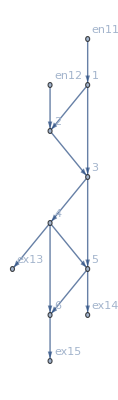

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
MFGEquations["FG"]
```

```mathematica
MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]
```

<|{1,1->2,1->3}→4/3,{1,1->2,en11->1}→0,{1,1->3,1->2}→0,{1,1->3,en11->1}→0,{1,en11->1,1->2}→0,{1,en11->1,1->3}→2,{2,1->2,2->3}→0,{2,1->2,en12->2}→0,{2,2->3,1->2}→0,{2,2->3,en12->2}→0,{2,en12->2,1->2}→4/3,{2,en12->2,2->3}→14/3,{3,1->3,2->3}→0,{3,1->3,3->4}→10/3-jt56,{3,1->3,3->5}→jt56,{3,2->3,1->3}→7/2-jt56-jt59,{3,2->3,3->4}→7/6+jt56,{3,2->3,3->5}→jt59,{3,3->4,1->3}→-7/2+jt56+jt59,{3,3->4,2->3}→0,{3,3->4,3->5}→7/2-jt56-jt59,{3,3->5,1->3}→0,{3,3->5,2->3}→0,{3,3->5,3->4}→0,{4,3->4,4->5}→0,{4,3->4,4->6}→jt67,{4,3->4,4->ex13}→9/2-jt67,{4,4->5,3->4}→0,{4,4->5,4->6}→1-jt67,{4,4->5,4->ex13}→jt67,{4,4->6,3->4}→0,{4,4->6,4->5}→0,{4,4->6,4->ex13}→0,{4,4->ex13,3->4}→0,{4,4->ex13,4->5}→0,{4,4->ex13,4->6}→0,{5,3->5,4->5}→1,{5,3->5,5->6}→2,{5,3->5,5->ex14}→1/2,{5,4->5,3->5}→0,{5,4->5,5->6}→0,{5,4->5,5->ex14}→0,{5,5->6,3->5}→0,{5,5->6,4->5}→0,{5,5->6,5->ex14}→0,{5,5->ex14,3->5}→0,{5,5->ex14,4->5}→0,{5,5->ex14,5->6}→0,{6,4->6,5->6}→0,{6,4->6,6->ex15}→1,{6,5->6,4->6}→0,{6,5->6,6->ex15}→2,{6,6->ex15,4->6}→0,{6,6->ex15,5->6}→0|>

```mathematica
MFGEquations["criticalreduced1"][[1]]//Reduce
```

(jt56==0&&jt59==7/2&&0≤jt67≤1)||(jt56==10/3&&jt59==1/6&&0≤jt67≤1)||(1/6≤jt59≤7/2&&jt56==1/2 (7-2 jt59)&&0≤jt67≤1)

#### Non-linear case

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

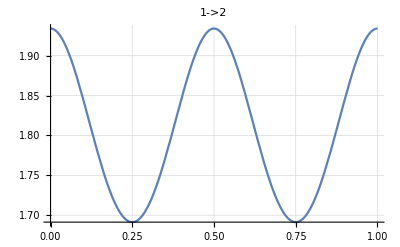
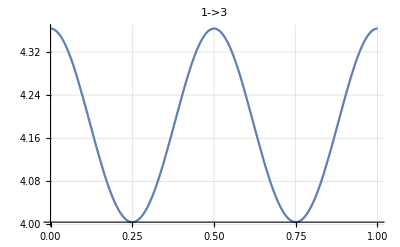
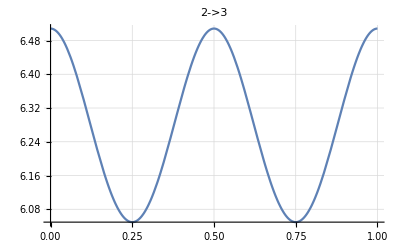
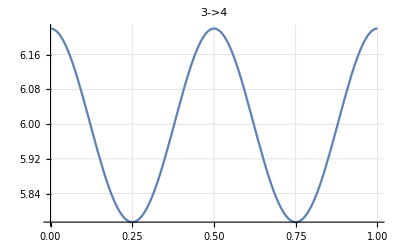
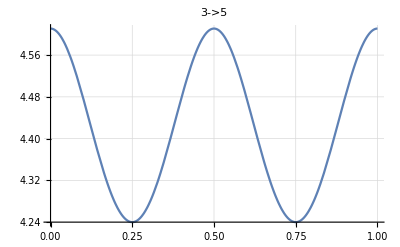
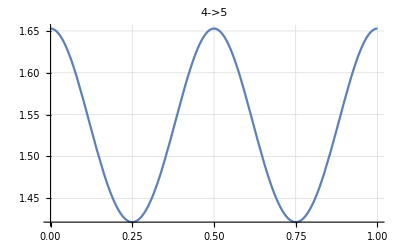
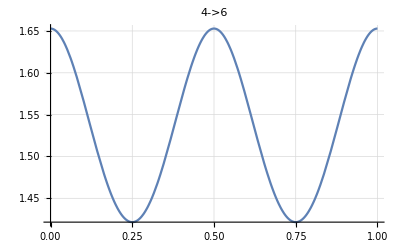
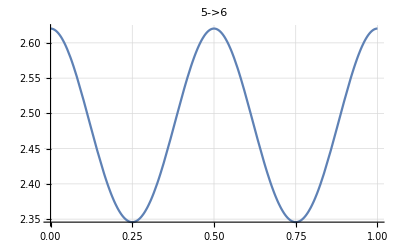

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,(*PlotRange->{-0.1,2.4},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,(*PlotRange->{1-0.1,4.7},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
H
V
W
```

Function[{x,p,m,edge},p^2/(2 m^alpha)+V[x,edge]-g[m]]

Function[{x,edge},W[x,A]]

Function[{x,a},a Sin[2 π (x+1/4)]^2]

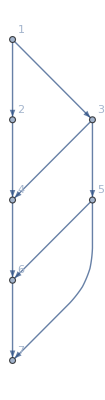
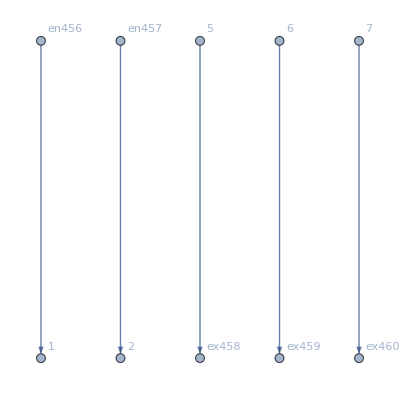
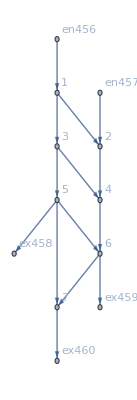
```mathematica
MFGEquations=<|"BG"->-Graphics-,"EntranceVertices"->{1,2},"InwardVertices"-><|1->en456,2->en457|>,"InEdges"->{en456->1,en457->2},"ExitVertices"->{5,6,7},"OutwardVertices"-><|5->ex458,6->ex459,7->ex460|>,"OutEdges"->{5->ex458,6->ex459,7->ex460},"AuxiliaryGraph"->-Graphics-,"FG"->-Graphics-,"VL"->{1,2,3,4,5,6,7},"EL"->{1->2,1->3,2->4,3->4,3->5,4->6,5->6,5->7,5->ex458,6->7,6->ex459,7->ex460,en456->1,en457->2},"BEL"->{1->2,1->3,2->4,3->4,3->5,4->6,5->6,5->7,6->7},"FVL"->{1,2,3,4,5,6,7,en456,en457,ex458,ex459,ex460},"AllTransitions"->{{1,1->2,1->3},{1,1->2,en456->1},{1,1->3,1->2},{1,1->3,en456->1},{1,en456->1,1->2},{1,en456->1,1->3},{2,1->2,2->4},{2,1->2,en457->2},{2,2->4,1->2},{2,2->4,en457->2},{2,en457->2,1->2},{2,en457->2,2->4},{3,1->3,3->4},{3,1->3,3->5},{3,3->4,1->3},{3,3->4,3->5},{3,3->5,1->3},{3,3->5,3->4},{4,2->4,3->4},{4,2->4,4->6},{4,3->4,2->4},{4,3->4,4->6},{4,4->6,2->4},{4,4->6,3->4},{5,3->5,5->6},{5,3->5,5->7},{5,3->5,5->ex458},{5,5->6,3->5},{5,5->6,5->7},{5,5->6,5->ex458},{5,5->7,3->5},{5,5->7,5->6},{5,5->7,5->ex458},{5,5->ex458,3->5},{5,5->ex458,5->6},{5,5->ex458,5->7},{6,4->6,5->6},{6,4->6,6->7},{6,4->6,6->ex459},{6,5->6,4->6},{6,5->6,6->7},{6,5->6,6->ex459},{6,6->7,4->6},{6,6->7,5->6},{6,6->7,6->ex459},{6,6->ex459,4->6},{6,6->ex459,5->6},{6,6->ex459,6->7},{7,5->7,6->7},{7,5->7,7->ex460},{7,6->7,5->7},{7,6->7,7->ex460},{7,7->ex460,5->7},{7,7->ex460,6->7}},"NoDeadEnds"->{{1,1->2},{1,1->3},{1,en456->1},{2,1->2},{2,2->4},{2,en457->2},{3,1->3},{3,3->4},{3,3->5},{4,2->4},{4,3->4},{4,4->6},{5,3->5},{5,5->6},{5,5->7},{5,5->ex458},{6,4->6},{6,5->6},{6,6->7},{6,6->ex459},{7,5->7},{7,6->7},{7,7->ex460}},"NoDeadStarts"->{{2,1->2},{3,1->3},{en456,en456->1},{1,1->2},{4,2->4},{en457,en457->2},{1,1->3},{4,3->4},{5,3->5},{2,2->4},{3,3->4},{6,4->6},{3,3->5},{6,5->6},{7,5->7},{ex458,5->ex458},{4,4->6},{5,5->6},{7,6->7},{ex459,6->ex459},{5,5->7},{6,6->7},{ex460,7->ex460}},"jargs"->{{2,1->2},{3,1->3},{4,2->4},{4,3->4},{5,3->5},{6,4->6},{6,5->6},{7,5->7},{ex458,5->ex458},{7,6->7},{ex459,6->ex459},{ex460,7->ex460},{1,en456->1},{2,en457->2},{1,1->2},{1,1->3},{2,2->4},{3,3->4},{3,3->5},{4,4->6},{5,5->6},{5,5->7},{5,5->ex458},{6,6->7},{6,6->ex459},{7,7->ex460},{en456,en456->1},{en457,en457->2}},"js"->{j461,j462,j463,j464,j465,j466,j467,j468,j469,j470,j471,j472,j473,j474,j475,j476,j477,j478,j479,j480,j481,j482,j483,j484,j485,j486,j487,j488},"jvars"-><|{2,1->2}->j461,{3,1->3}->j462,{4,2->4}->j463,{4,3->4}->j464,{5,3->5}->j465,{6,4->6}->j466,{6,5->6}->j467,{7,5->7}->j468,{ex458,5->ex458}->j469,{7,6->7}->j470,{ex459,6->ex459}->j471,{ex460,7->ex460}->j472,{1,en456->1}->j473,{2,en457->2}->j474,{1,1->2}->j475,{1,1->3}->j476,{2,2->4}->j477,{3,3->4}->j478,{3,3->5}->j479,{4,4->6}->j480,{5,5->6}->j481,{5,5->7}->j482,{5,5->ex458}->j483,{6,6->7}->j484,{6,6->ex459}->j485,{7,7->ex460}->j486,{en456,en456->1}->j487,{en457,en457->2}->j488|>,"jts"->{jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498,jt499,jt500,jt501,jt502,jt503,jt504,jt505,jt506,jt507,jt508,jt509,jt510,jt511,jt512,jt513,jt514,jt515,jt516,jt517,jt518,jt519,jt520,jt521,jt522,jt523,jt524,jt525,jt526,jt527,jt528,jt529,jt530,jt531,jt532,jt533,jt534,jt535,jt536,jt537,jt538,jt539,jt540,jt541,jt542},"jtvars"-><|{1,1->2,1->3}->jt489,{1,1->2,en456->1}->jt490,{1,1->3,1->2}->jt491,{1,1->3,en456->1}->jt492,{1,en456->1,1->2}->jt493,{1,en456->1,1->3}->jt494,{2,1->2,2->4}->jt495,{2,1->2,en457->2}->jt496,{2,2->4,1->2}->jt497,{2,2->4,en457->2}->jt498,{2,en457->2,1->2}->jt499,{2,en457->2,2->4}->jt500,{3,1->3,3->4}->jt501,{3,1->3,3->5}->jt502,{3,3->4,1->3}->jt503,{3,3->4,3->5}->jt504,{3,3->5,1->3}->jt505,{3,3->5,3->4}->jt506,{4,2->4,3->4}->jt507,{4,2->4,4->6}->jt508,{4,3->4,2->4}->jt509,{4,3->4,4->6}->jt510,{4,4->6,2->4}->jt511,{4,4->6,3->4}->jt512,{5,3->5,5->6}->jt513,{5,3->5,5->7}->jt514,{5,3->5,5->ex458}->jt515,{5,5->6,3->5}->jt516,{5,5->6,5->7}->jt517,{5,5->6,5->ex458}->jt518,{5,5->7,3->5}->jt519,{5,5->7,5->6}->jt520,{5,5->7,5->ex458}->jt521,{5,5->ex458,3->5}->jt522,{5,5->ex458,5->6}->jt523,{5,5->ex458,5->7}->jt524,{6,4->6,5->6}->jt525,{6,4->6,6->7}->jt526,{6,4->6,6->ex459}->jt527,{6,5->6,4->6}->jt528,{6,5->6,6->7}->jt529,{6,5->6,6->ex459}->jt530,{6,6->7,4->6}->jt531,{6,6->7,5->6}->jt532,{6,6->7,6->ex459}->jt533,{6,6->ex459,4->6}->jt534,{6,6->ex459,5->6}->jt535,{6,6->ex459,6->7}->jt536,{7,5->7,6->7}->jt537,{7,5->7,7->ex460}->jt538,{7,6->7,5->7}->jt539,{7,6->7,7->ex460}->jt540,{7,7->ex460,5->7}->jt541,{7,7->ex460,6->7}->jt542|>,"uargs"->{{1,1->2},{1,1->3},{2,2->4},{3,3->4},{3,3->5},{4,4->6},{5,5->6},{5,5->7},{5,5->ex458},{6,6->7},{6,6->ex459},{7,7->ex460},{en456,en456->1},{en457,en457->2},{2,1->2},{3,1->3},{4,2->4},{4,3->4},{5,3->5},{6,4->6},{6,5->6},{7,5->7},{ex458,5->ex458},{7,6->7},{ex459,6->ex459},{ex460,7->ex460},{1,en456->1},{2,en457->2}},"us"->{u543,u544,u545,u546,u547,u548,u549,u550,u551,u552,u553,u554,u555,u556,u557,u558,u559,u560,u561,u562,u563,u564,u565,u566,u567,u568,u569,u570},"uvars"-><|{1,1->2}->u543,{1,1->3}->u544,{2,2->4}->u545,{3,3->4}->u546,{3,3->5}->u547,{4,4->6}->u548,{5,5->6}->u549,{5,5->7}->u550,{5,5->ex458}->u551,{6,6->7}->u552,{6,6->ex459}->u553,{7,7->ex460}->u554,{en456,en456->1}->u555,{en457,en457->2}->u556,{2,1->2}->u557,{3,1->3}->u558,{4,2->4}->u559,{4,3->4}->u560,{5,3->5}->u561,{6,4->6}->u562,{6,5->6}->u563,{7,5->7}->u564,{ex458,5->ex458}->u565,{7,6->7}->u566,{ex459,6->ex459}->u567,{ex460,7->ex460}->u568,{1,en456->1}->u569,{2,en457->2}->u570|>,"SwitchingCosts"-><|{1,1->2,1->3}->0,{1,1->2,en456->1}->∞,{1,1->3,1->2}->0,{1,1->3,en456->1}->∞,{1,en456->1,1->2}->0,{1,en456->1,1->3}->0,{2,1->2,2->4}->0,{2,1->2,en457->2}->∞,{2,2->4,1->2}->0,{2,2->4,en457->2}->∞,{2,en457->2,1->2}->0,{2,en457->2,2->4}->0,{3,1->3,3->4}->0,{3,1->3,3->5}->0,{3,3->4,1->3}->0,{3,3->4,3->5}->0,{3,3->5,1->3}->0,{3,3->5,3->4}->0,{4,2->4,3->4}->0,{4,2->4,4->6}->0,{4,3->4,2->4}->0,{4,3->4,4->6}->0,{4,4->6,2->4}->0,{4,4->6,3->4}->0,{5,3->5,5->6}->0,{5,3->5,5->7}->0,{5,3->5,5->ex458}->0,{5,5->6,3->5}->0,{5,5->6,5->7}->0,{5,5->6,5->ex458}->0,{5,5->7,3->5}->0,{5,5->7,5->6}->0,{5,5->7,5->ex458}->0,{5,5->ex458,3->5}->∞,{5,5->ex458,5->6}->∞,{5,5->ex458,5->7}->∞,{6,4->6,5->6}->0,{6,4->6,6->7}->0,{6,4->6,6->ex459}->0,{6,5->6,4->6}->0,{6,5->6,6->7}->0,{6,5->6,6->ex459}->0,{6,6->7,4->6}->0,{6,6->7,5->6}->0,{6,6->7,6->ex459}->0,{6,6->ex459,4->6}->∞,{6,6->ex459,5->6}->∞,{6,6->ex459,6->7}->∞,{7,5->7,6->7}->0,{7,5->7,7->ex460}->0,{7,6->7,5->7}->0,{7,6->7,7->ex460}->0,{7,7->ex460,5->7}->∞,{7,7->ex460,6->7}->∞,{5,5->ex458,1->2}->∞,{5,5->ex458,1->3}->∞,{5,5->ex458,2->4}->∞,{5,5->ex458,3->4}->∞,{5,5->ex458,4->6}->∞,{5,5->ex458,5->ex458}->∞,{5,5->ex458,6->7}->∞,{5,5->ex458,6->ex459}->∞,{5,5->ex458,7->ex460}->∞,{5,5->ex458,en456->1}->∞,{5,5->ex458,en457->2}->∞,{6,6->ex459,1->2}->∞,{6,6->ex459,1->3}->∞,{6,6->ex459,2->4}->∞,{6,6->ex459,3->4}->∞,{6,6->ex459,3->5}->∞,{6,6->ex459,5->7}->∞,{6,6->ex459,5->ex458}->∞,{6,6->ex459,6->ex459}->∞,{6,6->ex459,7->ex460}->∞,{6,6->ex459,en456->1}->∞,{6,6->ex459,en457->2}->∞,{7,7->ex460,1->2}->∞,{7,7->ex460,1->3}->∞,{7,7->ex460,2->4}->∞,{7,7->ex460,3->4}->∞,{7,7->ex460,3->5}->∞,{7,7->ex460,4->6}->∞,{7,7->ex460,5->6}->∞,{7,7->ex460,5->ex458}->∞,{7,7->ex460,6->ex459}->∞,{7,7->ex460,7->ex460}->∞,{7,7->ex460,en456->1}->∞,{7,7->ex460,en457->2}->∞,{2,1->3,en457->2}->∞,{1,en456->1,en456->1}->∞,{2,en456->1,en457->2}->∞,{1,2->4,en456->1}->∞,{1,en457->2,en456->1}->∞,{2,en457->2,en457->2}->∞|>,"OutRules"->{{5,5->ex458,1->2}->∞,{5,5->ex458,1->3}->∞,{5,5->ex458,2->4}->∞,{5,5->ex458,3->4}->∞,{5,5->ex458,3->5}->∞,{5,5->ex458,4->6}->∞,{5,5->ex458,5->6}->∞,{5,5->ex458,5->7}->∞,{5,5->ex458,5->ex458}->∞,{5,5->ex458,6->7}->∞,{5,5->ex458,6->ex459}->∞,{5,5->ex458,7->ex460}->∞,{5,5->ex458,en456->1}->∞,{5,5->ex458,en457->2}->∞,{6,6->ex459,1->2}->∞,{6,6->ex459,1->3}->∞,{6,6->ex459,2->4}->∞,{6,6->ex459,3->4}->∞,{6,6->ex459,3->5}->∞,{6,6->ex459,4->6}->∞,{6,6->ex459,5->6}->∞,{6,6->ex459,5->7}->∞,{6,6->ex459,5->ex458}->∞,{6,6->ex459,6->7}->∞,{6,6->ex459,6->ex459}->∞,{6,6->ex459,7->ex460}->∞,{6,6->ex459,en456->1}->∞,{6,6->ex459,en457->2}->∞,{7,7->ex460,1->2}->∞,{7,7->ex460,1->3}->∞,{7,7->ex460,2->4}->∞,{7,7->ex460,3->4}->∞,{7,7->ex460,3->5}->∞,{7,7->ex460,4->6}->∞,{7,7->ex460,5->6}->∞,{7,7->ex460,5->7}->∞,{7,7->ex460,5->ex458}->∞,{7,7->ex460,6->7}->∞,{7,7->ex460,6->ex459}->∞,{7,7->ex460,7->ex460}->∞,{7,7->ex460,en456->1}->∞,{7,7->ex460,en457->2}->∞},"InRules"->{{1,1->2,en456->1}->∞,{2,1->2,en457->2}->∞,{1,1->3,en456->1}->∞,{2,1->3,en457->2}->∞,{1,en456->1,en456->1}->∞,{2,en456->1,en457->2}->∞,{1,1->2,en456->1}->∞,{2,1->2,en457->2}->∞,{1,2->4,en456->1}->∞,{2,2->4,en457->2}->∞,{1,en457->2,en456->1}->∞,{2,en457->2,en457->2}->∞},"EntryArgs"->{{1,en456->1},{2,en457->2}},"EntryDataAssociation"-><|{1,en456->1}->1,{2,en457->2}->2|>,"jays"-><|1->2->j461-j475,1->3->j462-j476,2->4->j463-j477,3->4->j464-j478,3->5->j465-j479,4->6->j466-j480,5->6->j467-j481,5->7->j468-j482,6->7->j470-j484|>,"NonZeroEntryCurrents"->True,"ExitCosts"-><|ex458->1,ex459->2,ex460->3|>,"EqCurrentCompCon"->(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0),"EqTransitionCompCon"->(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0),"EqCompCon"->(jt489==0||-u543+u544==0)&&jt490==0&&(jt491==0||u543-u544==0)&&jt492==0&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&jt496==0&&(jt497==0||-u545+u557==0)&&jt498==0&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&jt522==0&&jt523==0&&jt524==0&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&jt534==0&&jt535==0&&jt536==0&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&jt541==0&&jt542==0,"EqAllComp"->(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0)&&(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0)&&(jt489==0||-u543+u544==0)&&jt490==0&&(jt491==0||u543-u544==0)&&jt492==0&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&jt496==0&&(jt497==0||-u545+u557==0)&&jt498==0&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&jt522==0&&jt523==0&&jt524==0&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&jt534==0&&jt535==0&&jt536==0&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&jt541==0&&jt542==0,"EqPosCon"->NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542],"EqBalanceSplittingCurrents"->j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542,"EqBalanceGatheringCurrents"->j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540,"EqEntryIn"->j473==1&&j474==2,"EqExitValues"->u565==1&&u567==2&&u568==3,"EqSwitchingConditions"->NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566],"EqValueAuxiliaryEdges"->-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0,"EqAll"->NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542]&&j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542&&j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540&&j473==1&&j474==2&&u565==1&&u567==2&&u568==3&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0,"EqAllAll"->NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542]&&j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542&&j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540&&j473==1&&j474==2&&u565==1&&u567==2&&u568==3&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0&&(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0)&&(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0)&&(jt489==0||-u543+u544==0)&&jt490==0&&(jt491==0||u543-u544==0)&&jt492==0&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&jt496==0&&(jt497==0||-u545+u557==0)&&jt498==0&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&jt522==0&&jt523==0&&jt524==0&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&jt534==0&&jt535==0&&jt536==0&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&jt541==0&&jt542==0,"BoundaryRules"->{j473->1,j474->2,u565->1,u567->2,u568->3},"RulesEntryIn"->{j473->1,j474->2},"RulesExitValues"->{u565->1,u567->2,u568->3},"Nlhs"->{j461-j475-u543+u557,j462-j476-u544+u558,j463-j477-u545+u559,j464-j478-u546+u560,j465-j479-u547+u561,j466-j480-u548+u562,j467-j481-u549+u563,j468-j482-u550+u564,j470-j484-u552+u566},"EqCriticalCase"->j461-j475-u543+u557==0&&j462-j476-u544+u558==0&&j463-j477-u545+u559==0&&j464-j478-u546+u560==0&&j465-j479-u547+u561==0&&j466-j480-u548+u562==0&&j467-j481-u549+u563==0&&j468-j482-u550+u564==0&&j470-j484-u552+u566==0,"criticalreduced1"->{True,<|j461->0,j462->59/41,j465->72/41,j469->3,j472->0,j473->1,j474->2,j475->18/41,j476->0,j477->0,j478->13/41,j479->0,j481->34/41,j482->17/41,j483->0,j485->0,j486->0,j487->0,j488->0,jt489->18/41,jt490->0,jt491->0,jt492->0,jt493->0,jt494->1,jt496->0,jt497->0,jt498->0,jt499->18/41,jt500->64/41,jt503->0,jt504->13/41,jt505->0,jt506->0,jt507->13/41,jt509->0,jt510->0,jt512->0,jt515->72/41,jt517->0,jt518->34/41,jt520->0,jt521->17/41,jt522->0,jt523->0,jt524->0,jt525->34/41,jt527->0,jt528->0,jt529->0,jt530->0,jt533->0,jt534->0,jt535->0,jt536->0,jt537->0,jt538->0,jt540->0,jt541->0,jt542->0,u551->1,u553->2,u554->3,u557->190/41,u558->113/41,u559->126/41,u560->126/41,u561->1,u562->75/41,u563->75/41,u564->58/41,u565->1,u566->58/41,u567->2,u568->3,u569->172/41,u570->190/41,j463->64/41,j464->0,j466->51/41,j467->0,j468->0,j470->17/41,j471->0,j480->0,j484->0,jt495->0,jt501->0,jt502->59/41,jt508->51/41,jt511->0,jt513->0,jt514->0,jt516->0,jt519->0,jt526->17/41,jt531->0,jt532->0,jt539->17/41,u543->172/41,u544->172/41,u545->190/41,u546->113/41,u547->113/41,u548->126/41,u549->1,u550->1,u552->75/41,u555->172/41,u556->190/41|>},"Nrhs"->{j461-j475+IntM[j461-j475,1->2],j462-j476+IntM[j462-j476,1->3],j463-j477+IntM[j463-j477,2->4],j464-j478+IntM[j464-j478,3->4],j465-j479+IntM[j465-j479,3->5],j466-j480+IntM[j466-j480,4->6],j467-j481+IntM[j467-j481,5->6],j468-j482+IntM[j468-j482,5->7],j470-j484+IntM[j470-j484,6->7]},"EqGeneralCase"->j461-j475-u543+u557==j461-j475+IntM[j461-j475,1->2]&&j462-j476-u544+u558==j462-j476+IntM[j462-j476,1->3]&&j463-j477-u545+u559==j463-j477+IntM[j463-j477,2->4]&&j464-j478-u546+u560==j464-j478+IntM[j464-j478,3->4]&&j465-j479-u547+u561==j465-j479+IntM[j465-j479,3->5]&&j466-j480-u548+u562==j466-j480+IntM[j466-j480,4->6]&&j467-j481-u549+u563==j467-j481+IntM[j467-j481,5->6]&&j468-j482-u550+u564==j468-j482+IntM[j468-j482,5->7]&&j470-j484-u552+u566==j470-j484+IntM[j470-j484,6->7],"TOL"->1/1000000|>;
```